```mathematica
optsLabel1=Sequence[FontFamily->"Helvetica",FontSize->22];
optsLabel2=Sequence[FontFamily->"Helvetica",FontSize->22,Transparent];
optsCentrality=Sequence[FontFamily->"Helvetica",FontSize->18];
optsCentrality2=Sequence[FontFamily->"Helvetica",FontSize->18,Transparent];
optsScale1=Sequence[FontFamily->"Helvetica",FontSize->16];
optsScale2=Sequence[FontFamily->"Helvetica",FontSize->16,Transparent];
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Mdata={{8.385269122,4528.301887},{29.91501416,6367.924528},{53.93767705,9056.603774}}
```

{{8.38527,4528.3},{29.915,6367.92},{53.9377,9056.6}}

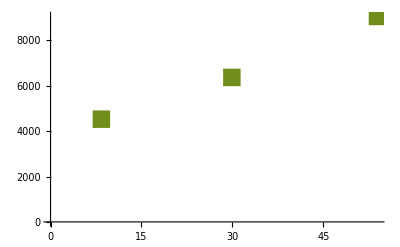

```mathematica
dataM=ListPlot[Mdata,PlotMarkers->{"■",18},PlotStyle->Darker[Blend[{Yellow,Pink,Green}]]]
```

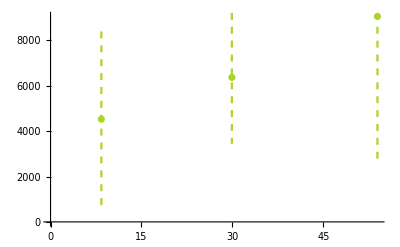

```mathematica
largeErrorsM=ErrorListPlot[{{{8.385269122,4528.301887},ErrorBar[{-3915.09434,3867.924528}]},{{29.91501416,6367.924528},ErrorBar[{-2924.528302,5990.566038}]},{{53.93767705,9056.603774},ErrorBar[{-6415.09434,11415.09434}]}}, PlotStyle->{Blend[{Yellow,Pink,Green}],Dashed}]
```

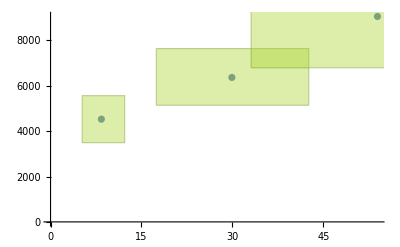

```mathematica
smallErrorsM=ErrorListPlot[{{{8.385269122,4528.301887},ErrorBar[{-3.172804533,3.852691218},{-1037.735849,1037.735849}]},{{29.91501416,6367.924528},ErrorBar[{-12.46458924,12.691218130},{-1226.41509,1273.584906}]},{{53.93767705,9056.603774},ErrorBar[{-20.84985836,21.07648725},{-2264.150943,2547.169811}]}},ErrorBarFunction->Function[{coords, errs}, {Blend[{Yellow,Pink,Green}],Opacity[0.4],EdgeForm[Directive[Thin,Darker[Blend[{Yellow,Pink,Green}]]]],Rectangle[coords+{errs⟦1,1⟧,errs⟦2,1⟧},coords+{errs⟦1,2⟧,errs⟦2,2⟧}]}]]
```

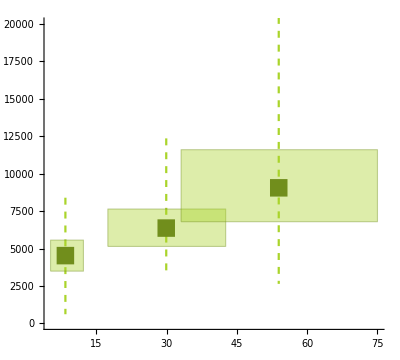

```mathematica
PlotM=Show[largeErrorsM,smallErrorsM,dataM,PlotRange->{0,20000},AspectRatio->0.9]
```

```mathematica
Rdata={{8.385269122,3140.877598},{29.91501416,13302.54042},{53.93767705,35473.44111}}
```

{{8.38527,3140.88},{29.915,13302.5},{53.9377,35473.4}}

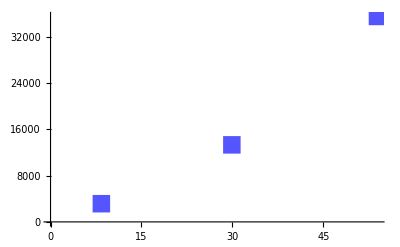

```mathematica
dataR=ListPlot[Rdata,PlotMarkers->{"■",18},PlotStyle->Lighter[Blue]]
```

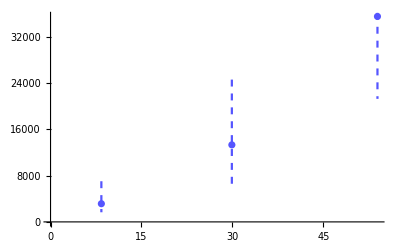

```mathematica
largeErrorsR=ErrorListPlot[{{{8.385269122,3140.877598},ErrorBar[{-1478.060046,3879.907621}]},{{29.91501416,13302.54042},ErrorBar[{-7759.815242,11270.20785}]},{{53.93767705,35473.44111},ErrorBar[{-14226.32794,22170.90069}]}}, PlotStyle->{Lighter[Blue],Dashed}]
```

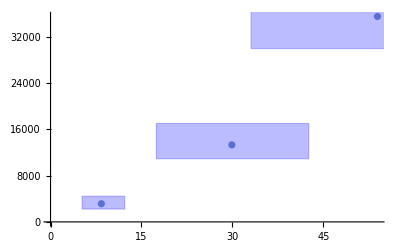

```mathematica
smallErrorsR=ErrorListPlot[{{{8.385269122,3140.877598},ErrorBar[{-3.172804533,3.852691218},{-923.7875289,1293.30254}]},{{29.91501416,13302.54042},ErrorBar[{-12.46458924,12.691218130},{-2401.847575,3695.150115}]},{{53.93767705,35473.44111},ErrorBar[{-20.84985836,21.07648725},{-5542.725173,8683.602771}]}},ErrorBarFunction->Function[{coords, errs}, {Lighter[Blue],Opacity[0.4],EdgeForm[Directive[Thin,Lighter[Blue]]],Rectangle[coords+{errs⟦1,1⟧,errs⟦2,1⟧},coords+{errs⟦1,2⟧,errs⟦2,2⟧}]}]]
```

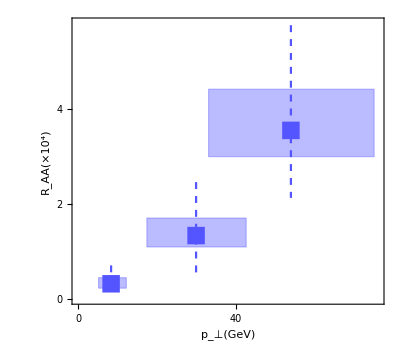

```mathematica
PlotR=Show[largeErrorsR,smallErrorsR,dataR,PlotRange->{{0,76},{0,58000}},Frame->True,FrameLabel->{StyleForm["p_⊥(GeV)",optsLabel1],StyleForm["R_AA(×10^4)",optsLabel1]},FrameTicks->{
{{{0,StyleForm["0",optsScale1],{0.03,0}},{20000,StyleForm["2",optsScale1],{0.03,0}},{40000,StyleForm["4",optsScale1],{0.03,0}},{60000,StyleForm["6",optsScale1],{0.03,0}}},None},

{{{0,StyleForm["0",optsScale1],{0.03,0}},{20,StyleForm["20",optsScale1],{0.03,0}},{40,StyleForm["40",optsScale1],{0.03,0}},{60,StyleForm["60",optsScale1],{0.03,0}},{80,StyleForm["80",optsScale1],{0.03,0}},{100,StyleForm["100",optsScale1],{0.03,0}}},None}
},AspectRatio->0.9]
```

```mathematica
MRdata={{8.385269122,1.136801541},{29.91501416,0.467244701},{53.93767705,0.226396917}}
```

{{8.38527,1.1368},{29.915,0.467245},{53.9377,0.226397}}

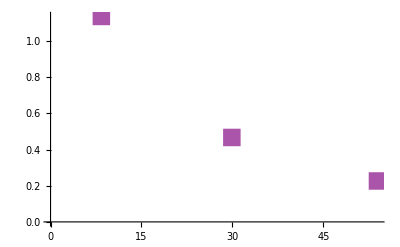

```mathematica
dataMR=ListPlot[MRdata,PlotMarkers->{"■",18},PlotStyle->Lighter[Purple]]
```

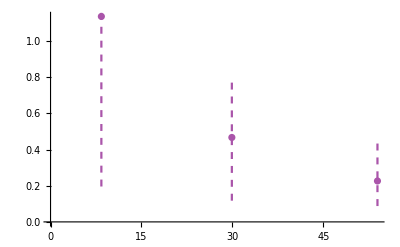

```mathematica
largeErrorsMR=ErrorListPlot[{{{8.385269122,1.136801541},ErrorBar[{-0.968208092,0.968208092}]},{{29.91501416,0.467244701},ErrorBar[{-0.356454721,0.303468208}]},{{53.93767705,0.226396917},ErrorBar[{-0.173410405,0.207129094}]}}, PlotStyle->{Lighter[Purple],Dashed}]
```

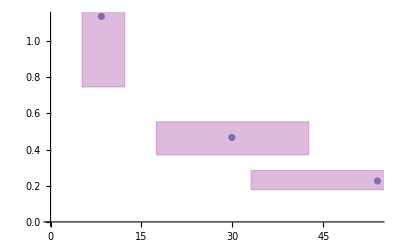

```mathematica
smallErrorsMR=ErrorListPlot[{{{8.385269122,1.136801541},ErrorBar[{-3.172804533,3.852691218},{-0.39017341,0.289017341}]},{{29.91501416,0.467244701},ErrorBar[{-12.46458924,12.691218130},{-0.096339114,0.086705202}]},{{53.93767705,0.226396917},ErrorBar[{-20.84985836,21.07648725},{-0.048169557,0.057803468}]}},ErrorBarFunction->Function[{coords, errs}, {Lighter[Purple],Opacity[0.4],EdgeForm[Directive[Thin,Lighter[Purple]]],Rectangle[coords+{errs⟦1,1⟧,errs⟦2,1⟧},coords+{errs⟦1,2⟧,errs⟦2,2⟧}]}]]
```

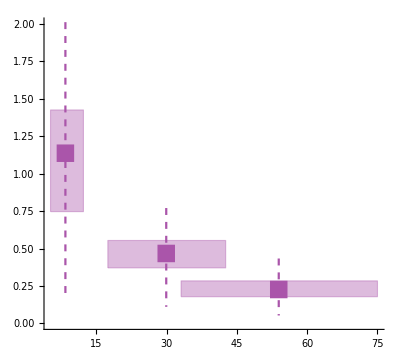

```mathematica
PlotRatioMR=Show[largeErrorsMR,smallErrorsMR,dataMR,PlotRange->{0,2},AspectRatio->0.9]
```

```mathematica
Clear[c,ct,α,ω,p,s,ϕMC,KRC,γ]
```

```mathematica
c=α/4(√(1+(8ct)/α)-1)
```

1/4 (-1+√(1+(8 ct)/α)) α

```mathematica
α=√(1600/5.6)
ω=130.
p=25.
γ=5.1
M=(ϕMC r1)/(1+c^2 γ)
R=KRC ct
```

16.9031

130.

25.

5.1

(r1 ϕMC)/(1+91.0714 (-1+√(1+0.473286 ct))^2)

ct KRC

```mathematica
s=0.2
```

0.2

```mathematica
Clear[r1]
```

```mathematica
ee=Table[{r1,NSolve[-ct/r1+s+((-1+√(1+(8 ct)/α))^2 α^2)/(16 (1+1/16 (1+1/p) (-1+√(1+(8 ct)/α))^2 α^2+((-1+√(1+(8 ct)/α))^4 α^4 ω)/(256 p)))==0,ct,Reals]},{r1,0.05,5,0.05}]
```

{{0.05,{{ct→0.010005}}},{0.1,{{ct→0.02004}}},{0.15,{{ct→0.0301351}}},{0.2,{{ct→0.0403216}}},{0.25,{{ct→0.0506316}}},{0.3,{{ct→0.0610998}}},{0.35,{{ct→0.071763}}},{0.4,{{ct→0.0826618}}},{0.45,{{ct→0.0938412}}},{0.5,{{ct→0.105352}}},{0.55,{{ct→0.117251}}},{0.6,{{ct→0.129605}}},{0.65,{{ct→0.14249}}},{0.7,{{ct→0.155997}}},{0.75,{{ct→0.170232}}},{0.8,{{ct→0.185324}}},{0.85,{{ct→0.201422}}},{0.9,{{ct→0.218707}}},{0.95,{{ct→0.237391}}},{1.,{{ct→0.257711}}},{1.05,{{ct→0.27992}}},{1.1,{{ct→0.304241}}},{1.15,{{ct→0.330793}}},{1.2,{{ct→0.359469}}},{1.25,{{ct→0.389833}}},{1.3,{{ct→0.421127}}},{1.35,{{ct→0.452459}}},{1.4,{{ct→0.483058}}},{1.45,{{ct→0.512429}}},{1.5,{{ct→0.540349}}},{1.55,{{ct→0.566788}}},{1.6,{{ct→0.591819}}},{1.65,{{ct→0.61556}}},{1.7,{{ct→0.638141}}},{1.75,{{ct→0.65969}}},{1.8,{{ct→0.68032}}},{1.85,{{ct→0.700133}}},{1.9,{{ct→0.719219}}},{1.95,{{ct→0.737653}}},{2.,{{ct→0.755504}}},{2.05,{{ct→0.772827}}},{2.1,{{ct→0.789675}}},{2.15,{{ct→0.806089}}},{2.2,{{ct→0.822109}}},{2.25,{{ct→0.837768}}},{2.3,{{ct→0.853096}}},{2.35,{{ct→0.868118}}},{2.4,{{ct→0.88286}}},{2.45,{{ct→0.897341}}},{2.5,{{ct→0.91158}}},{2.55,{{ct→0.925593}}},{2.6,{{ct→0.939398}}},{2.65,{{ct→0.953006}}},{2.7,{{ct→0.96643}}},{2.75,{{ct→0.979683}}},{2.8,{{ct→0.992774}}},{2.85,{{ct→1.00571}}},{2.9,{{ct→1.01851}}},{2.95,{{ct→1.03117}}},{3.,{{ct→1.0437}}},{3.05,{{ct→1.05611}}},{3.1,{{ct→1.06841}}},{3.15,{{ct→1.08059}}},{3.2,{{ct→1.09268}}},{3.25,{{ct→1.10466}}},{3.3,{{ct→1.11656}}},{3.35,{{ct→1.12836}}},{3.4,{{ct→1.14008}}},{3.45,{{ct→1.15172}}},{3.5,{{ct→1.16328}}},{3.55,{{ct→1.17476}}},{3.6,{{ct→1.18618}}},{3.65,{{ct→1.19753}}},{3.7,{{ct→1.20881}}},{3.75,{{ct→1.22003}}},{3.8,{{ct→1.23119}}},{3.85,{{ct→1.2423}}},{3.9,{{ct→1.25335}}},{3.95,{{ct→1.26435}}},{4.,{{ct→1.2753}}},{4.05,{{ct→1.28619}}},{4.1,{{ct→1.29705}}},{4.15,{{ct→1.30785}}},{4.2,{{ct→1.31862}}},{4.25,{{ct→1.32934}}},{4.3,{{ct→1.34002}}},{4.35,{{ct→1.35067}}},{4.4,{{ct→1.36127}}},{4.45,{{ct→1.37184}}},{4.5,{{ct→1.38238}}},{4.55,{{ct→1.39288}}},{4.6,{{ct→1.40335}}},{4.65,{{ct→1.41379}}},{4.7,{{ct→1.4242}}},{4.75,{{ct→1.43458}}},{4.8,{{ct→1.44493}}},{4.85,{{ct→1.45526}}},{4.9,{{ct→1.46556}}},{4.95,{{ct→1.47583}}},{5.,{{ct→1.48608}}}}

```mathematica
ee1={{0.05,0.010004992660182807},{0.1,0.02003995400391828},{0.15000000000000002,0.030135128765694758},{0.2,0.040321556513526195},{0.25,0.05063163971306113},{0.3,0.06109976123439873},{0.35000000000000003,0.07176297800175944},{0.4,0.08266182204213712},{0.45,0.09384124670001326},{0.5,0.10535176448102519},{0.55,0.11725083394296083},{0.6000000000000001,0.12960456579821472},{0.6500000000000001,0.14248983102608864},{0.7000000000000001,0.15599686099988572},{0.7500000000000001,0.17023241834022143},{0.8,0.18532355726191183},{0.8500000000000001,0.20142181696775163},{0.9000000000000001,0.21870726014920436},{0.9500000000000001,0.23739080111544383},{1.,0.2577112767326708},{1.05,0.2799200998680365},{1.1,0.3042413165108567},{1.1500000000000001,0.3307927559912502},{1.2000000000000002,0.3594686075988203},{1.2500000000000002,0.38983261865776986},{1.3,0.42112712559743265},{1.35,0.4524590237789055},{1.4000000000000001,0.4830578099804275},{1.4500000000000002,0.5124285034594241},{1.5000000000000002,0.5403491913699293},{1.55,0.5667883230481805},{1.6,0.591819012245014},{1.6500000000000001,0.6155598193295879},{1.7000000000000002,0.6381412996859311},{1.7500000000000002,0.6596896080559541},{1.8,0.6803196593627023},{1.85,0.700133135809406},{1.9000000000000001,0.7192187463961562},{1.9500000000000002,0.7376534100970256},{2.,0.7555037180728231},{2.05,0.772827381324468},{2.1,0.789674543997336},{2.15,0.8060889255601295},{2.1999999999999997,0.8221087926623775},{2.25,0.8377677767985126},{2.3,0.8530955586376168},{2.35,0.8681184398155635},{2.4,0.8828598209685902},{2.45,0.8973406021669125},{2.5,0.9115795192968815},{2.55,0.9255934275904429},{2.6,0.9393975414877807},{2.65,0.953005638340751},{2.7,0.9664302320866218},{2.75,0.9796827218996307},{2.8,0.9927735199183605},{2.85,1.0057121614108893},{2.9,1.0185074001439998},{2.95,1.031167291240038},{3.,1.043699263413078},{3.05,1.056110182156971},{3.1,1.0684064051973272},{3.15,1.0805938313060695},{3.2,1.0926779434018},{3.25,1.1046638467145709},{3.3,1.1165563026739351},{3.35,1.1283597590797452},{3.4,1.140078377032324},{3.45,1.151716055029363},{3.5,1.163276450578793},{3.55,1.1747629996279592},{3.6,1.1861789340681341},{3.65,1.1975272975384137},{3.7,1.2088109597233239},{3.75,1.2200326293131376},{3.8,1.231194865774254},{3.85,1.2423000900584438},{3.9,1.253350594363829},{3.95,1.2643485510467218},{4.,1.2752960207715935},{4.05,1.286194959976164},{4.1,1.2970472277196854},{4.15,1.3078545919747349},{4.2,1.3186187354160634},{4.25,1.3293412607541268},{4.3,1.3400236956557534},{4.35,1.350667497289846},{4.4,1.3612740565320185},{4.45,1.3718447018585425},{4.5,1.3823807029568678},{4.55,1.3928832740772186},{4.6,1.4033535771473407},{4.65,1.4137927246702913},{4.7,1.4242017824232522},{4.75,1.4345817719736156},{4.8,1.4449336730270734},{4.8500000000000005,1.4552584256210601},{4.9,1.4655569321756814},{4.95,1.4758300594131617},{5.,1.4860786401558512}};
```

```mathematica
Nmax=Length[ee1]
```

100

```mathematica
ϕMC=12500.
KRC=44000.
```

12500.

44000.

```mathematica
RTable=Table[{ee1[[i,1]],KRC ee1[[i,2]]},{i,1,Nmax}]
```

{{0.05,440.22},{0.1,881.758},{0.15,1325.95},{0.2,1774.15},{0.25,2227.79},{0.3,2688.39},{0.35,3157.57},{0.4,3637.12},{0.45,4129.01},{0.5,4635.48},{0.55,5159.04},{0.6,5702.6},{0.65,6269.55},{0.7,6863.86},{0.75,7490.23},{0.8,8154.24},{0.85,8862.56},{0.9,9623.12},{0.95,10445.2},{1.,11339.3},{1.05,12316.5},{1.1,13386.6},{1.15,14554.9},{1.2,15816.6},{1.25,17152.6},{1.3,18529.6},{1.35,19908.2},{1.4,21254.5},{1.45,22546.9},{1.5,23775.4},{1.55,24938.7},{1.6,26040.},{1.65,27084.6},{1.7,28078.2},{1.75,29026.3},{1.8,29934.1},{1.85,30805.9},{1.9,31645.6},{1.95,32456.8},{2.,33242.2},{2.05,34004.4},{2.1,34745.7},{2.15,35467.9},{2.2,36172.8},{2.25,36861.8},{2.3,37536.2},{2.35,38197.2},{2.4,38845.8},{2.45,39483.},{2.5,40109.5},{2.55,40726.1},{2.6,41333.5},{2.65,41932.2},{2.7,42522.9},{2.75,43106.},{2.8,43682.},{2.85,44251.3},{2.9,44814.3},{2.95,45371.4},{3.,45922.8},{3.05,46468.8},{3.1,47009.9},{3.15,47546.1},{3.2,48077.8},{3.25,48605.2},{3.3,49128.5},{3.35,49647.8},{3.4,50163.4},{3.45,50675.5},{3.5,51184.2},{3.55,51689.6},{3.6,52191.9},{3.65,52691.2},{3.7,53187.7},{3.75,53681.4},{3.8,54172.6},{3.85,54661.2},{3.9,55147.4},{3.95,55631.3},{4.,56113.},{4.05,56592.6},{4.1,57070.1},{4.15,57545.6},{4.2,58019.2},{4.25,58491.},{4.3,58961.},{4.35,59429.4},{4.4,59896.1},{4.45,60361.2},{4.5,60824.8},{4.55,61286.9},{4.6,61747.6},{4.65,62206.9},{4.7,62664.9},{4.75,63121.6},{4.8,63577.1},{4.85,64031.4},{4.9,64484.5},{4.95,64936.5},{5.,65387.5}}

```mathematica
MTable=Table[{ee1[[i,1]],(ee1[[i,1]] ϕMC)/(1+14.492753623188404 (-1+√(1+0.5253570214625479 ee1[[i,2]]))^2 γ)},{i,1,Nmax}]
```

{{0.05,624.682},{0.1,1247.46},{0.15,1866.42},{0.2,2479.65},{0.25,3085.19},{0.3,3681.02},{0.35,4265.04},{0.4,4835.07},{0.45,5388.77},{0.5,5923.66},{0.55,6437.06},{0.6,6926.05},{0.65,7387.41},{0.7,7817.6},{0.75,8212.65},{0.8,8568.12},{0.85,8879.05},{0.9,9139.92},{0.95,9344.72},{1.,9487.23},{1.05,9561.6},{1.1,9563.65},{1.15,9493.02},{1.2,9355.84},{1.25,9166.51},{1.3,8946.19},{1.35,8717.29},{1.4,8497.51},{1.45,8297.16},{1.5,8120.14},{1.55,7966.39},{1.6,7833.91},{1.65,7720.03},{1.7,7622.09},{1.75,7537.64},{1.8,7464.6},{1.85,7401.18},{1.9,7345.91},{1.95,7297.56},{2.,7255.1},{2.05,7217.68},{2.1,7184.58},{2.15,7155.21},{2.2,7129.06},{2.25,7105.7},{2.3,7084.77},{2.35,7065.95},{2.4,7048.99},{2.45,7033.64},{2.5,7019.71},{2.55,7007.02},{2.6,6995.43},{2.65,6984.81},{2.7,6975.03},{2.75,6966.01},{2.8,6957.64},{2.85,6949.85},{2.9,6942.58},{2.95,6935.75},{3.,6929.33},{3.05,6923.24},{3.1,6917.47},{3.15,6911.95},{3.2,6906.67},{3.25,6901.59},{3.3,6896.68},{3.35,6891.92},{3.4,6887.29},{3.45,6882.76},{3.5,6878.32},{3.55,6873.96},{3.6,6869.65},{3.65,6865.39},{3.7,6861.17},{3.75,6856.97},{3.8,6852.78},{3.85,6848.6},{3.9,6844.42},{3.95,6840.23},{4.,6836.03},{4.05,6831.82},{4.1,6827.57},{4.15,6823.31},{4.2,6819.01},{4.25,6814.67},{4.3,6810.3},{4.35,6805.89},{4.4,6801.44},{4.45,6796.95},{4.5,6792.41},{4.55,6787.82},{4.6,6783.19},{4.65,6778.51},{4.7,6773.78},{4.75,6769.},{4.8,6764.17},{4.85,6759.29},{4.9,6754.36},{4.95,6749.37},{5.,6744.34}}

```mathematica
MRRatio=Table[{ee1[[i,1]],(ee1[[i,1]] ϕMC)/(ee1[[i,2]] KRC (1+14.492753623188404 (-1+√(1+0.5253570214625479 ee1[[i,2]]))^2 γ))},{i,1,Nmax}]
```

{{0.05,1.41902},{0.1,1.41474},{0.15,1.40762},{0.2,1.39766},{0.25,1.38487},{0.3,1.36923},{0.35,1.35074},{0.4,1.32937},{0.45,1.3051},{0.5,1.2779},{0.55,1.24773},{0.6,1.21454},{0.65,1.1783},{0.7,1.13895},{0.75,1.09645},{0.8,1.05076},{0.85,1.00186},{0.9,0.949787},{0.95,0.894643},{1.,0.836668},{1.05,0.776325},{1.1,0.714419},{1.15,0.652223},{1.2,0.59152},{1.25,0.534408},{1.3,0.482805},{1.35,0.437874},{1.4,0.399798},{1.45,0.367996},{1.5,0.341536},{1.55,0.319439},{1.6,0.300841},{1.65,0.285034},{1.7,0.271459},{1.75,0.259683},{1.8,0.249368},{1.85,0.240252},{1.9,0.23213},{1.95,0.22484},{2.,0.21825},{2.05,0.212257},{2.1,0.206776},{2.15,0.201738},{2.2,0.197084},{2.25,0.192766},{2.3,0.188745},{2.35,0.184986},{2.4,0.181461},{2.45,0.178144},{2.5,0.175014},{2.55,0.172052},{2.6,0.169244},{2.65,0.166574},{2.7,0.16403},{2.75,0.161602},{2.8,0.159279},{2.85,0.157054},{2.9,0.154919},{2.95,0.152866},{3.,0.150891},{3.05,0.148987},{3.1,0.147149},{3.15,0.145374},{3.2,0.143656},{3.25,0.141993},{3.3,0.140381},{3.35,0.138816},{3.4,0.137297},{3.45,0.13582},{3.5,0.134384},{3.55,0.132985},{3.6,0.131623},{3.65,0.130295},{3.7,0.128999},{3.75,0.127734},{3.8,0.126499},{3.85,0.125292},{3.9,0.124111},{3.95,0.122956},{4.,0.121826},{4.05,0.120719},{4.1,0.119635},{4.15,0.118572},{4.2,0.11753},{4.25,0.116508},{4.3,0.115505},{4.35,0.114521},{4.4,0.113554},{4.45,0.112605},{4.5,0.111672},{4.55,0.110755},{4.6,0.109854},{4.65,0.108967},{4.7,0.108095},{4.75,0.107237},{4.8,0.106393},{4.85,0.105562},{4.9,0.104744},{4.95,0.103938},{5.,0.103144}}

```mathematica
RR=Interpolation[RTable]
```

InterpolatingFunction[…]

```mathematica
MM=Interpolation[MTable]
```

InterpolatingFunction[…]

```mathematica
MR=Interpolation[MRRatio]
```

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {0.0000680952} lies outside the range of data in the interpolating function. Extrapolation will be used.

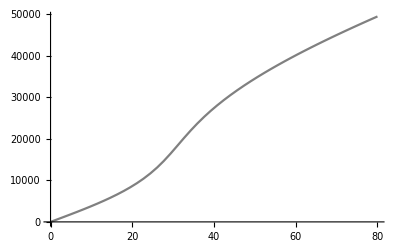

```mathematica
RRPlot20=Plot[RR[x/24],{x,0,80},PlotStyle->{Gray}]
```

InterpolatingFunction::dmval: Input value {0.0000680952} lies outside the range of data in the interpolating function. Extrapolation will be used.

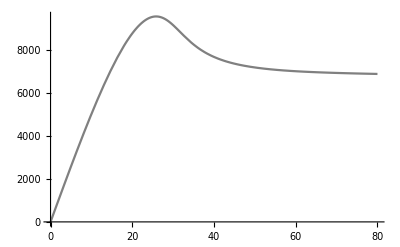

```mathematica
MMPlot20=Plot[MM[x/24],{x,0,80},PlotRange->All,PlotStyle->{Gray}]
```

InterpolatingFunction::dmval: Input value {0.0000680952} lies outside the range of data in the interpolating function. Extrapolation will be used.

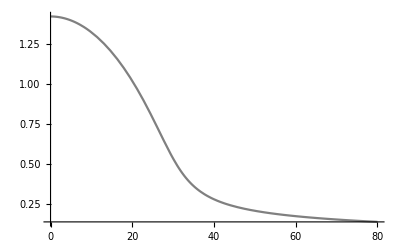

```mathematica
MRPlot20=Plot[MR[x/24],{x,0,80},PlotRange->All,PlotStyle->{Gray}]
```

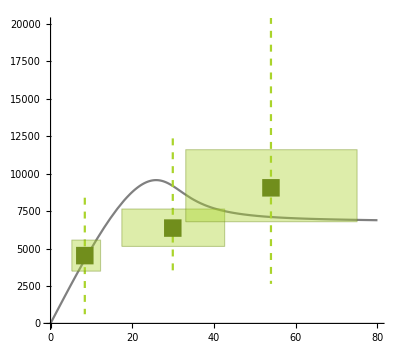

```mathematica
PlotM=Show[MMPlot20,largeErrorsM,smallErrorsM,dataM,PlotRange->{0,20000},AspectRatio->0.9]
```

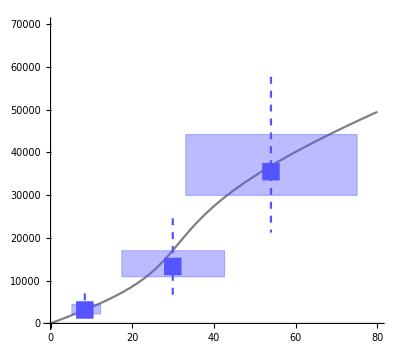

```mathematica
PlotR=Show[RRPlot20,largeErrorsR,smallErrorsR,dataR,PlotRange->{0,70000},AspectRatio->0.9]
```

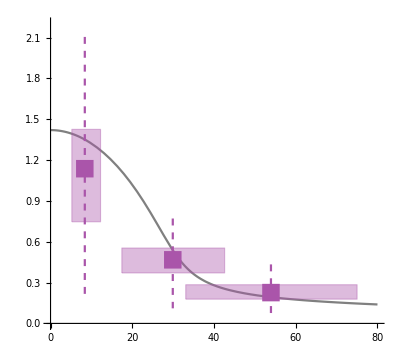

```mathematica
PlotRatioMR=Show[MRPlot20,largeErrorsMR,smallErrorsMR,dataMR,PlotRange->{0,2.2},AxesOrigin->{0,0},AspectRatio->0.9]
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

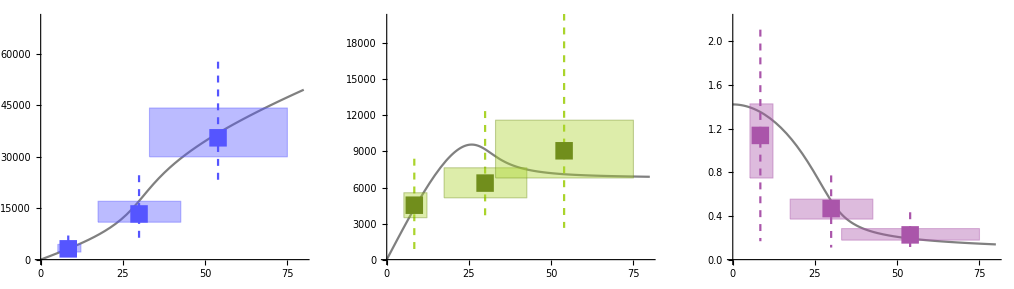

```mathematica
GraphicsArray[{PlotR,PlotM,PlotRatioMR}]
```

Here we reproduce Supplementary Figure S2:

```mathematica
s=0.02
```

0.02

```mathematica
ϕMC=7000.
KRC=250000.
```

7000.

250000.

```mathematica
ee=Table[{r1,NSolve[-ct/r1+s+((-1+√(1+(8 ct)/α))^2 α^2)/(16 (1+1/16 (1+1/p) (-1+√(1+(8 ct)/α))^2 α^2+((-1+√(1+(8 ct)/α))^4 α^4 ω)/(256 p)))==0,ct,Reals]},{r1,0.05,5,0.01}]
```

{{0.05,{{ct→0.00100005}}},{0.06,{{ct→0.00120009}}},{0.07,{{ct→0.00140014}}},{0.08,{{ct→0.0016002}}},{0.09,{{ct→0.00180029}}},{0.1,{{ct→0.0020004}}},{0.11,{{ct→0.00220053}}},{0.12,{{ct→0.00240069}}},{0.13,{{ct→0.00260088}}},{0.14,{{ct→0.0028011}}},{0.15,{{ct→0.00300135}}},{0.16,{{ct→0.00320164}}},{0.17,{{ct→0.00340197}}},{0.18,{{ct→0.00360233}}},{0.19,{{ct→0.00380275}}},{0.2,{{ct→0.0040032}}},{0.21,{{ct→0.00420371}}},{0.22,{{ct→0.00440426}}},{0.23,{{ct→0.00460487}}},{0.24,{{ct→0.00480554}}},{0.25,{{ct→0.00500626}}},{0.26,{{ct→0.00520704}}},{0.27,{{ct→0.00540789}}},{0.28,{{ct→0.0056088}}},{0.29,{{ct→0.00580977}}},{0.3,{{ct→0.00601082}}},{0.31,{{ct→0.00621194}}},{0.32,{{ct→0.00641314}}},{0.33,{{ct→0.00661441}}},{0.34,{{ct→0.00681577}}},{0.35,{{ct→0.0070172}}},{0.36,{{ct→0.00721873}}},{0.37,{{ct→0.00742034}}},{0.38,{{ct→0.00762204}}},{0.39,{{ct→0.00782383}}},{0.4,{{ct→0.00802571}}},{0.41,{{ct→0.0082277}}},{0.42,{{ct→0.00842978}}},{0.43,{{ct→0.00863197}}},{0.44,{{ct→0.00883427}}},{0.45,{{ct→0.00903667}}},{0.46,{{ct→0.00923918}}},{0.47,{{ct→0.0094418}}},{0.48,{{ct→0.00964454}}},{0.49,{{ct→0.0098474}}},{0.5,{{ct→0.0100504}}},{0.51,{{ct→0.0102535}}},{0.52,{{ct→0.0104567}}},{0.53,{{ct→0.0106601}}},{0.54,{{ct→0.0108636}}},{0.55,{{ct→0.0110672}}},{0.56,{{ct→0.0112709}}},{0.57,{{ct→0.0114748}}},{0.58,{{ct→0.0116789}}},{0.59,{{ct→0.0118831}}},{0.6,{{ct→0.0120874}}},{0.61,{{ct→0.0122919}}},{0.62,{{ct→0.0124965}}},{0.63,{{ct→0.0127013}}},{0.64,{{ct→0.0129063}}},{0.65,{{ct→0.0131114}}},{0.66,{{ct→0.0133167}}},{0.67,{{ct→0.0135221}}},{0.68,{{ct→0.0137277}}},{0.69,{{ct→0.0139335}}},{0.7,{{ct→0.0141395}}},{0.71,{{ct→0.0143456}}},{0.72,{{ct→0.0145519}}},{0.73,{{ct→0.0147584}}},{0.74,{{ct→0.0149651}}},{0.75,{{ct→0.015172}}},{0.76,{{ct→0.0153791}}},{0.77,{{ct→0.0155863}}},{0.78,{{ct→0.0157938}}},{0.79,{{ct→0.0160015}}},{0.8,{{ct→0.0162093}}},{0.81,{{ct→0.0164174}}},{0.82,{{ct→0.0166257}}},{0.83,{{ct→0.0168342}}},{0.84,{{ct→0.0170429}}},{0.85,{{ct→0.0172519}}},{0.86,{{ct→0.017461}}},{0.87,{{ct→0.0176704}}},{0.88,{{ct→0.0178801}}},{0.89,{{ct→0.0180899}}},{0.9,{{ct→0.0183}}},{0.91,{{ct→0.0185103}}},{0.92,{{ct→0.0187209}}},{0.93,{{ct→0.0189317}}},{0.94,{{ct→0.0191428}}},{0.95,{{ct→0.0193541}}},{0.96,{{ct→0.0195657}}},{0.97,{{ct→0.0197775}}},{0.98,{{ct→0.0199896}}},{0.99,{{ct→0.0202019}}},{1.,{{ct→0.0204146}}},{1.01,{{ct→0.0206275}}},{1.02,{{ct→0.0208406}}},{1.03,{{ct→0.0210541}}},{1.04,{{ct→0.0212678}}},{1.05,{{ct→0.0214819}}},{1.06,{{ct→0.0216962}}},{1.07,{{ct→0.0219108}}},{1.08,{{ct→0.0221257}}},{1.09,{{ct→0.0223409}}},{1.1,{{ct→0.0225564}}},{1.11,{{ct→0.0227722}}},{1.12,{{ct→0.0229884}}},{1.13,{{ct→0.0232048}}},{1.14,{{ct→0.0234216}}},{1.15,{{ct→0.0236387}}},{1.16,{{ct→0.0238561}}},{1.17,{{ct→0.0240738}}},{1.18,{{ct→0.0242919}}},{1.19,{{ct→0.0245103}}},{1.2,{{ct→0.0247291}}},{1.21,{{ct→0.0249482}}},{1.22,{{ct→0.0251677}}},{1.23,{{ct→0.0253875}}},{1.24,{{ct→0.0256077}}},{1.25,{{ct→0.0258282}}},{1.26,{{ct→0.0260492}}},{1.27,{{ct→0.0262704}}},{1.28,{{ct→0.0264921}}},{1.29,{{ct→0.0267142}}},{1.3,{{ct→0.0269366}}},{1.31,{{ct→0.0271594}}},{1.32,{{ct→0.0273826}}},{1.33,{{ct→0.0276062}}},{1.34,{{ct→0.0278303}}},{1.35,{{ct→0.0280547}}},{1.36,{{ct→0.0282795}}},{1.37,{{ct→0.0285048}}},{1.38,{{ct→0.0287305}}},{1.39,{{ct→0.0289566}}},{1.4,{{ct→0.0291831}}},{1.41,{{ct→0.0294101}}},{1.42,{{ct→0.0296375}}},{1.43,{{ct→0.0298654}}},{1.44,{{ct→0.0300937}}},{1.45,{{ct→0.0303225}}},{1.46,{{ct→0.0305517}}},{1.47,{{ct→0.0307814}}},{1.48,{{ct→0.0310116}}},{1.49,{{ct→0.0312422}}},{1.5,{{ct→0.0314734}}},{1.51,{{ct→0.031705}}},{1.52,{{ct→0.0319371}}},{1.53,{{ct→0.0321698}}},{1.54,{{ct→0.0324029}}},{1.55,{{ct→0.0326365}}},{1.56,{{ct→0.0328707}}},{1.57,{{ct→0.0331054}}},{1.58,{{ct→0.0333406}}},{1.59,{{ct→0.0335763}}},{1.6,{{ct→0.0338126}}},{1.61,{{ct→0.0340495}}},{1.62,{{ct→0.0342869}}},{1.63,{{ct→0.0345248}}},{1.64,{{ct→0.0347633}}},{1.65,{{ct→0.0350024}}},{1.66,{{ct→0.0352421}}},{1.67,{{ct→0.0354823}}},{1.68,{{ct→0.0357232}}},{1.69,{{ct→0.0359646}}},{1.7,{{ct→0.0362067}}},{1.71,{{ct→0.0364493}}},{1.72,{{ct→0.0366926}}},{1.73,{{ct→0.0369365}}},{1.74,{{ct→0.0371811}}},{1.75,{{ct→0.0374263}}},{1.76,{{ct→0.0376721}}},{1.77,{{ct→0.0379186}}},{1.78,{{ct→0.0381658}}},{1.79,{{ct→0.0384136}}},{1.8,{{ct→0.0386621}}},{1.81,{{ct→0.0389113}}},{1.82,{{ct→0.0391612}}},{1.83,{{ct→0.0394118}}},{1.84,{{ct→0.0396631}}},{1.85,{{ct→0.0399151}}},{1.86,{{ct→0.0401679}}},{1.87,{{ct→0.0404214}}},{1.88,{{ct→0.0406756}}},{1.89,{{ct→0.0409306}}},{1.9,{{ct→0.0411864}}},{1.91,{{ct→0.0414429}}},{1.92,{{ct→0.0417002}}},{1.93,{{ct→0.0419583}}},{1.94,{{ct→0.0422172}}},{1.95,{{ct→0.0424769}}},{1.96,{{ct→0.0427375}}},{1.97,{{ct→0.0429988}}},{1.98,{{ct→0.043261}}},{1.99,{{ct→0.0435241}}},{2.,{{ct→0.043788}}},{2.01,{{ct→0.0440528}}},{2.02,{{ct→0.0443185}}},{2.03,{{ct→0.044585}}},{2.04,{{ct→0.0448525}}},{2.05,{{ct→0.0451209}}},{2.06,{{ct→0.0453902}}},{2.07,{{ct→0.0456604}}},{2.08,{{ct→0.0459317}}},{2.09,{{ct→0.0462038}}},{2.1,{{ct→0.046477}}},{2.11,{{ct→0.0467511}}},{2.12,{{ct→0.0470262}}},{2.13,{{ct→0.0473023}}},{2.14,{{ct→0.0475795}}},{2.15,{{ct→0.0478577}}},{2.16,{{ct→0.048137}}},{2.17,{{ct→0.0484173}}},{2.18,{{ct→0.0486987}}},{2.19,{{ct→0.0489812}}},{2.2,{{ct→0.0492648}}},{2.21,{{ct→0.0495495}}},{2.22,{{ct→0.0498354}}},{2.23,{{ct→0.0501224}}},{2.24,{{ct→0.0504106}}},{2.25,{{ct→0.0507}}},{2.26,{{ct→0.0509906}}},{2.27,{{ct→0.0512824}}},{2.28,{{ct→0.0515754}}},{2.29,{{ct→0.0518697}}},{2.3,{{ct→0.0521652}}},{2.31,{{ct→0.0524621}}},{2.32,{{ct→0.0527602}}},{2.33,{{ct→0.0530597}}},{2.34,{{ct→0.0533605}}},{2.35,{{ct→0.0536627}}},{2.36,{{ct→0.0539662}}},{2.37,{{ct→0.0542712}}},{2.38,{{ct→0.0545776}}},{2.39,{{ct→0.0548854}}},{2.4,{{ct→0.0551947}}},{2.41,{{ct→0.0555055}}},{2.42,{{ct→0.0558177}}},{2.43,{{ct→0.0561315}}},{2.44,{{ct→0.0564469}}},{2.45,{{ct→0.0567639}}},{2.46,{{ct→0.0570824}}},{2.47,{{ct→0.0574026}}},{2.48,{{ct→0.0577244}}},{2.49,{{ct→0.0580479}}},{2.5,{{ct→0.0583731}}},{2.51,{{ct→0.0587}}},{2.52,{{ct→0.0590287}}},{2.53,{{ct→0.0593592}}},{2.54,{{ct→0.0596915}}},{2.55,{{ct→0.0600257}}},{2.56,{{ct→0.0603617}}},{2.57,{{ct→0.0606996}}},{2.58,{{ct→0.0610395}}},{2.59,{{ct→0.0613813}}},{2.6,{{ct→0.0617252}}},{2.61,{{ct→0.0620711}}},{2.62,{{ct→0.0624191}}},{2.63,{{ct→0.0627691}}},{2.64,{{ct→0.0631214}}},{2.65,{{ct→0.0634758}}},{2.66,{{ct→0.0638324}}},{2.67,{{ct→0.0641913}}},{2.68,{{ct→0.0645525}}},{2.69,{{ct→0.0649161}}},{2.7,{{ct→0.065282}}},{2.71,{{ct→0.0656504}}},{2.72,{{ct→0.0660213}}},{2.73,{{ct→0.0663947}}},{2.74,{{ct→0.0667707}}},{2.75,{{ct→0.0671493}}},{2.76,{{ct→0.0675306}}},{2.77,{{ct→0.0679146}}},{2.78,{{ct→0.0683014}}},{2.79,{{ct→0.0686911}}},{2.8,{{ct→0.0690836}}},{2.81,{{ct→0.0694792}}},{2.82,{{ct→0.0698777}}},{2.83,{{ct→0.0702794}}},{2.84,{{ct→0.0706841}}},{2.85,{{ct→0.0710922}}},{2.86,{{ct→0.0715035}}},{2.87,{{ct→0.0719181}}},{2.88,{{ct→0.0723362}}},{2.89,{{ct→0.0727579}}},{2.9,{{ct→0.0731831}}},{2.91,{{ct→0.073612}}},{2.92,{{ct→0.0740447},{ct→0.431934},{ct→0.47014}}},{2.93,{{ct→0.0744812},{ct→0.414932},{ct→0.487433}}},{2.94,{{ct→0.0749217},{ct→0.403749},{ct→0.498903}}},{2.95,{{ct→0.0753662},{ct→0.394781},{ct→0.508154}}},{2.96,{{ct→0.0758149},{ct→0.387081},{ct→0.516133}}},{2.97,{{ct→0.0762678},{ct→0.380231},{ct→0.523258}}},{2.98,{{ct→0.076725},{ct→0.373999},{ct→0.52976}}},{2.99,{{ct→0.0771868},{ct→0.368245},{ct→0.53578}}},{3.,{{ct→0.0776531},{ct→0.362872},{ct→0.541414}}},{3.01,{{ct→0.0781241},{ct→0.357814},{ct→0.546728}}},{3.02,{{ct→0.0786},{ct→0.353021},{ct→0.551773}}},{3.03,{{ct→0.0790808},{ct→0.348454},{ct→0.556587}}},{3.04,{{ct→0.0795667},{ct→0.344083},{ct→0.561199}}},{3.05,{{ct→0.0800578},{ct→0.339885},{ct→0.565633}}},{3.06,{{ct→0.0805544},{ct→0.33584},{ct→0.569909}}},{3.07,{{ct→0.0810564},{ct→0.33193},{ct→0.574044}}},{3.08,{{ct→0.0815642},{ct→0.328144},{ct→0.57805}}},{3.09,{{ct→0.0820779},{ct→0.324468},{ct→0.581939}}},{3.1,{{ct→0.0825976},{ct→0.320893},{ct→0.585721}}},{3.11,{{ct→0.0831236},{ct→0.31741},{ct→0.589405}}},{3.12,{{ct→0.083656},{ct→0.314011},{ct→0.592998}}},{3.13,{{ct→0.0841951},{ct→0.31069},{ct→0.596507}}},{3.14,{{ct→0.084741},{ct→0.307441},{ct→0.599937}}},{3.15,{{ct→0.085294},{ct→0.304257},{ct→0.603294}}},{3.16,{{ct→0.0858544},{ct→0.301135},{ct→0.606582}}},{3.17,{{ct→0.0864223},{ct→0.298069},{ct→0.609806}}},{3.18,{{ct→0.0869981},{ct→0.295057},{ct→0.612969}}},{3.19,{{ct→0.087582},{ct→0.292093},{ct→0.616075}}},{3.2,{{ct→0.0881743},{ct→0.289175},{ct→0.619126}}},{3.21,{{ct→0.0887754},{ct→0.2863},{ct→0.622126}}},{3.22,{{ct→0.0893856},{ct→0.283464},{ct→0.625077}}},{3.23,{{ct→0.0900052},{ct→0.280666},{ct→0.627982}}},{3.24,{{ct→0.0906347},{ct→0.277901},{ct→0.630843}}},{3.25,{{ct→0.0912743},{ct→0.275169},{ct→0.633661}}},{3.26,{{ct→0.0919246},{ct→0.272466},{ct→0.636438}}},{3.27,{{ct→0.092586},{ct→0.269791},{ct→0.639177}}},{3.28,{{ct→0.093259},{ct→0.267141},{ct→0.641879}}},{3.29,{{ct→0.0939442},{ct→0.264514},{ct→0.644546}}},{3.3,{{ct→0.094642},{ct→0.261909},{ct→0.647178}}},{3.31,{{ct→0.0953531},{ct→0.259323},{ct→0.649778}}},{3.32,{{ct→0.0960782},{ct→0.256754},{ct→0.652346}}},{3.33,{{ct→0.0968179},{ct→0.254201},{ct→0.654883}}},{3.34,{{ct→0.0975731},{ct→0.251662},{ct→0.657391}}},{3.35,{{ct→0.0983445},{ct→0.249135},{ct→0.659871}}},{3.36,{{ct→0.0991331},{ct→0.246618},{ct→0.662323}}},{3.37,{{ct→0.0999398},{ct→0.244109},{ct→0.664749}}},{3.38,{{ct→0.100766},{ct→0.241606},{ct→0.66715}}},{3.39,{{ct→0.101612},{ct→0.239107},{ct→0.669525}}},{3.4,{{ct→0.10248},{ct→0.236611},{ct→0.671877}}},{3.41,{{ct→0.103372},{ct→0.234114},{ct→0.674205}}},{3.42,{{ct→0.104288},{ct→0.231615},{ct→0.67651}}},{3.43,{{ct→0.105231},{ct→0.229111},{ct→0.678794}}},{3.44,{{ct→0.106203},{ct→0.2266},{ct→0.681057}}},{3.45,{{ct→0.107205},{ct→0.224078},{ct→0.683298}}},{3.46,{{ct→0.108241},{ct→0.221542},{ct→0.68552}}},{3.47,{{ct→0.109314},{ct→0.218989},{ct→0.687722}}},{3.48,{{ct→0.110427},{ct→0.216415},{ct→0.689905}}},{3.49,{{ct→0.111583},{ct→0.213816},{ct→0.692069}}},{3.5,{{ct→0.112789},{ct→0.211185},{ct→0.694216}}},{3.51,{{ct→0.114048},{ct→0.208518},{ct→0.696344}}},{3.52,{{ct→0.115368},{ct→0.205808},{ct→0.698456}}},{3.53,{{ct→0.116757},{ct→0.203045},{ct→0.70055}}},{3.54,{{ct→0.118225},{ct→0.200219},{ct→0.702629}}},{3.55,{{ct→0.119784},{ct→0.197318},{ct→0.704691}}},{3.56,{{ct→0.121451},{ct→0.194325},{ct→0.706738}}},{3.57,{{ct→0.123246},{ct→0.191218},{ct→0.708769}}},{3.58,{{ct→0.125198},{ct→0.187969},{ct→0.710786}}},{3.59,{{ct→0.127351},{ct→0.184534},{ct→0.712788}}},{3.6,{{ct→0.129767},{ct→0.180849},{ct→0.714776}}},{3.61,{{ct→0.132555},{ct→0.176807},{ct→0.71675}}},{3.62,{{ct→0.135919},{ct→0.172201},{ct→0.71871}}},{3.63,{{ct→0.140374},{ct→0.166518},{ct→0.720657}}},{3.64,{{ct→0.148984},{ct→0.156693},{ct→0.72259}}},{3.65,{{ct→0.724511}}},{3.66,{{ct→0.726419}}},{3.67,{{ct→0.728315}}},{3.68,{{ct→0.730199}}},{3.69,{{ct→0.732071}}},{3.7,{{ct→0.733932}}},{3.71,{{ct→0.735781}}},{3.72,{{ct→0.737619}}},{3.73,{{ct→0.739445}}},{3.74,{{ct→0.741261}}},{3.75,{{ct→0.743067}}},{3.76,{{ct→0.744862}}},{3.77,{{ct→0.746647}}},{3.78,{{ct→0.748422}}},{3.79,{{ct→0.750186}}},{3.8,{{ct→0.751942}}},{3.81,{{ct→0.753687}}},{3.82,{{ct→0.755424}}},{3.83,{{ct→0.75715}}},{3.84,{{ct→0.758868}}},{3.85,{{ct→0.760577}}},{3.86,{{ct→0.762277}}},{3.87,{{ct→0.763969}}},{3.88,{{ct→0.765652}}},{3.89,{{ct→0.767326}}},{3.9,{{ct→0.768993}}},{3.91,{{ct→0.770651}}},{3.92,{{ct→0.772301}}},{3.93,{{ct→0.773943}}},{3.94,{{ct→0.775577}}},{3.95,{{ct→0.777204}}},{3.96,{{ct→0.778823}}},{3.97,{{ct→0.780435}}},{3.98,{{ct→0.782039}}},{3.99,{{ct→0.783636}}},{4.,{{ct→0.785226}}},{4.01,{{ct→0.786808}}},{4.02,{{ct→0.788384}}},{4.03,{{ct→0.789953}}},{4.04,{{ct→0.791515}}},{4.05,{{ct→0.79307}}},{4.06,{{ct→0.794619}}},{4.07,{{ct→0.796161}}},{4.08,{{ct→0.797697}}},{4.09,{{ct→0.799227}}},{4.1,{{ct→0.80075}}},{4.11,{{ct→0.802267}}},{4.12,{{ct→0.803777}}},{4.13,{{ct→0.805282}}},{4.14,{{ct→0.806781}}},{4.15,{{ct→0.808274}}},{4.16,{{ct→0.809761}}},{4.17,{{ct→0.811242}}},{4.18,{{ct→0.812717}}},{4.19,{{ct→0.814187}}},{4.2,{{ct→0.815652}}},{4.21,{{ct→0.81711}}},{4.22,{{ct→0.818564}}},{4.23,{{ct→0.820012}}},{4.24,{{ct→0.821454}}},{4.25,{{ct→0.822892}}},{4.26,{{ct→0.824324}}},{4.27,{{ct→0.825751}}},{4.28,{{ct→0.827173}}},{4.29,{{ct→0.82859}}},{4.3,{{ct→0.830002}}},{4.31,{{ct→0.831409}}},{4.32,{{ct→0.832811}}},{4.33,{{ct→0.834208}}},{4.34,{{ct→0.8356}}},{4.35,{{ct→0.836988}}},{4.36,{{ct→0.838371}}},{4.37,{{ct→0.83975}}},{4.38,{{ct→0.841123}}},{4.39,{{ct→0.842493}}},{4.4,{{ct→0.843858}}},{4.41,{{ct→0.845218}}},{4.42,{{ct→0.846574}}},{4.43,{{ct→0.847925}}},{4.44,{{ct→0.849273}}},{4.45,{{ct→0.850616}}},{4.46,{{ct→0.851954}}},{4.47,{{ct→0.853289}}},{4.48,{{ct→0.854619}}},{4.49,{{ct→0.855946}}},{4.5,{{ct→0.857268}}},{4.51,{{ct→0.858586}}},{4.52,{{ct→0.8599}}},{4.53,{{ct→0.86121}}},{4.54,{{ct→0.862517}}},{4.55,{{ct→0.863819}}},{4.56,{{ct→0.865117}}},{4.57,{{ct→0.866412}}},{4.58,{{ct→0.867703}}},{4.59,{{ct→0.86899}}},{4.6,{{ct→0.870273}}},{4.61,{{ct→0.871553}}},{4.62,{{ct→0.872829}}},{4.63,{{ct→0.874101}}},{4.64,{{ct→0.87537}}},{4.65,{{ct→0.876635}}},{4.66,{{ct→0.877897}}},{4.67,{{ct→0.879155}}},{4.68,{{ct→0.88041}}},{4.69,{{ct→0.881661}}},{4.7,{{ct→0.882909}}},{4.71,{{ct→0.884153}}},{4.72,{{ct→0.885394}}},{4.73,{{ct→0.886632}}},{4.74,{{ct→0.887866}}},{4.75,{{ct→0.889098}}},{4.76,{{ct→0.890325}}},{4.77,{{ct→0.89155}}},{4.78,{{ct→0.892772}}},{4.79,{{ct→0.89399}}},{4.8,{{ct→0.895205}}},{4.81,{{ct→0.896417}}},{4.82,{{ct→0.897626}}},{4.83,{{ct→0.898831}}},{4.84,{{ct→0.900034}}},{4.85,{{ct→0.901234}}},{4.86,{{ct→0.90243}}},{4.87,{{ct→0.903624}}},{4.88,{{ct→0.904815}}},{4.89,{{ct→0.906003}}},{4.9,{{ct→0.907187}}},{4.91,{{ct→0.908369}}},{4.92,{{ct→0.909548}}},{4.93,{{ct→0.910725}}},{4.94,{{ct→0.911898}}},{4.95,{{ct→0.913069}}},{4.96,{{ct→0.914236}}},{4.97,{{ct→0.915401}}},{4.98,{{ct→0.916563}}},{4.99,{{ct→0.917723}}},{5.,{{ct→0.91888}}}}

```mathematica
ее1Down={{0.05,0.001000049993117016},{0.060000000000000005,0.0012000863877791737},{0.07,0.001400137181160265},{0.08,0.0016002047743441372},{0.09,0.0018002915692902045},{0.1,0.002000399969023684},{0.11,0.0022005323778260142},{0.12000000000000001,0.002400691201425488},{0.13,0.0026008788471881474},{0.14,0.0028010977243089746},{0.15000000000000002,0.0030013502440034193},{0.16,0.0032016388196993077},{0.16999999999999998,0.003401965867229162},{0.18,0.003602333805022984},{0.19,0.003802745054301533},{0.2,0.004003202039270142},{0.21000000000000002,0.004203707187313112},{0.22000000000000003,0.004404262929188732},{0.22999999999999998,0.0046048716992249505},{0.24,0.0048055359355157565},{0.25,0.005006258080118303},{0.26,0.005207040579250816},{0.27,0.005407885883491329},{0.28,0.005608796447977297},{0.29,0.005809774732606111},{0.3,0.006010823202236587},{0.31,0.006211944326891436},{0.32,0.006413140581960798},{0.33,0.006614414448406849},{0.33999999999999997,0.006815768412969554},{0.35,0.007017204968373599},{0.36,0.007218726613536536},{0.37,0.007420335853778215},{0.38,0.00762203520103153},{0.39,0.007823827174054526},{0.4,0.008025714298643924},{0.41,0.008227699107850112},{0.42,0.00842978414219364},{0.43,0.00863197194988328},{0.44,0.008834265087035702},{0.45,0.009036666117896807},{0.46,0.009239177615064775},{0.47,0.009441802159714878},{0.48,0.009644542341826124},{0.49,0.009847400760409757},{0.5,0.010050380023739706},{0.51,0.010253482749584994},{0.52,0.010456711565444218},{0.53,0.010660069108782092},{0.54,0.010863558027268173},{0.55,0.01106718097901779},{0.56,0.011270940632835248},{0.5700000000000001,0.01147483966845937},{0.5800000000000001,0.011678880776811437},{0.5900000000000001,0.01188306666024558},{0.6000000000000001,0.012087400032801711},{0.6100000000000001,0.012291883620461035},{0.6200000000000001,0.012496520161404217},{0.63,0.01270131240627227},{0.64,0.01290626311843025},{0.65,0.013111375074233792},{0.66,0.013316651063298598},{0.67,0.013522093888772914},{0.68,0.013727706367613099},{0.6900000000000001,0.013933491330862347},{0.7000000000000001,0.014139451623932634},{0.7100000000000001,0.014345590106889973},{0.7200000000000001,0.014551909654743076},{0.7300000000000001,0.01475841315773546},{0.7400000000000001,0.014965103521641133},{0.7500000000000001,0.015171983668063892},{0.76,0.015379056534740369},{0.77,0.015586325075846867},{0.78,0.015793792262310116},{0.79,0.016001461082122012},{0.8,0.016209334540658444},{0.81,0.016417415661002306},{0.8200000000000001,0.01662570748427079},{0.8300000000000001,0.016834213069947045},{0.8400000000000001,0.01704293549621634},{0.8500000000000001,0.0172518778603068},{0.8600000000000001,0.017461043278834815},{0.8700000000000001,0.017670434888155298},{0.8800000000000001,0.017880055844716785},{0.89,0.018089909325421635},{0.9,0.018299998527991305},{0.91,0.01851032667133692},{0.92,0.018720896995935217},{0.93,0.018931712764209983},{0.9400000000000001,0.01914277726091913},{0.9500000000000001,0.01935409379354754},{0.9600000000000001,0.01956566569270579},{0.9700000000000001,0.019777496312534906},{0.9800000000000001,0.019989589031117302},{0.9900000000000001,0.020201947250894005},{1.,0.020414574399088364},{1.01,0.020627473928136346},{1.02,0.020840649316123595},{1.03,0.021054104067229424},{1.04,0.021267841712177847},{1.05,0.021481865808695898},{1.06,0.02169617994197931},{1.07,0.02191078772516583},{1.08,0.022125692799816243},{1.09,0.022340898836403365},{1.1,0.022556409534809158},{1.11,0.02277222862483016},{1.12,0.022988359866691413},{1.1300000000000001,0.02320480705156915},{1.1400000000000001,0.023421574002122334},{1.1500000000000001,0.02363866457303338},{1.1600000000000001,0.02385608265155821},{1.1700000000000002,0.024073832158085853},{1.1800000000000002,0.02429191704670788},{1.1900000000000002,0.02451034130579784},{1.2000000000000002,0.02472910895860097},{1.21,0.02494822406383444},{1.22,0.025167690716298347},{1.23,0.02538751304749776},{1.24,0.025607695226276032},{1.25,0.025828241459459726},{1.26,0.026049155992515345},{1.27,0.026270443110218245},{1.28,0.02649210713733398},{1.29,0.02671415243931236},{1.3,0.02693658342299462},{1.31,0.02715940453733394},{1.32,0.02738262027412967},{1.33,0.027606235168775653},{1.34,0.027830253801022914},{1.35,0.02805468079575713},{1.36,0.02827952082379125},{1.37,0.028504778602673638},{1.3800000000000001,0.0287304588975121},{1.3900000000000001,0.028956566521814272},{1.4000000000000001,0.029183106338344714},{1.4100000000000001,0.02941008325999919},{1.4200000000000002,0.02963750225069653},{1.4300000000000002,0.029865368326288572},{1.4400000000000002,0.030093686555488625},{1.4500000000000002,0.030322462060818938},{1.46,0.03055170001957767},{1.47,0.030781405664825904},{1.48,0.031011584286395156},{1.49,0.03124224123191602},{1.5,0.031473381907868435},{1.51,0.03170501178065415},{1.52,0.03193713637769208},{1.53,0.03216976128853698},{1.54,0.0324028921660223},{1.55,0.03263653472742766},{1.56,0.03287069475567177},{1.57,0.03310537810053137},{1.58,0.033340590679887046},{1.59,0.03357633848099649},{1.6,0.033812627561796135},{1.61,0.03404946405223182},{1.62,0.03428685415561937},{1.6300000000000001,0.03452480415003592},{1.6400000000000001,0.03476332038974282},{1.6500000000000001,0.035002409306641065},{1.6600000000000001,0.0352420774117601},{1.6700000000000002,0.035482331296781064},{1.6800000000000002,0.03572317763559536},{1.6900000000000002,0.03596462318589962},{1.7000000000000002,0.03620667479082813},{1.7100000000000002,0.03644933938062374},{1.72,0.0366926239743485},{1.73,0.0369365356816351},{1.74,0.03718108170448035},{1.75,0.03742626933908193},{1.76,0.03767210597771974},{1.77,0.037918599110683224},{1.78,0.038165756328245884},{1.79,0.038413585322688654},{1.8,0.03866209389037345},{1.81,0.038911289933868484},{1.82,0.039161181464127004},{1.83,0.03941177660272096},{1.84,0.03966308358413151},{1.85,0.03991511075809795},{1.86,0.04016786659202707},{1.87,0.040421359673464725},{1.8800000000000001,0.04067559871263169},{1.8900000000000001,0.040930592545025776},{1.9000000000000001,0.04118635013409242},{1.9100000000000001,0.04144288057396596},{1.9200000000000002,0.04170019309228375},{1.9300000000000002,0.04195829705307574},{1.9400000000000002,0.04221720195973182},{1.9500000000000002,0.04247691745804956},{1.9600000000000002,0.04273745333936502},{1.97,0.04299881954376944},{1.98,0.043261026163414686},{1.99,0.04352408344591038},{2.,0.04378800179781603},{2.01,0.04405279178823116},{2.02,0.0443184641524871},{2.03,0.044585029795943726},{2.04,0.04485249979789493},{2.05,0.04512088541558664},{2.06,0.04539019808835136},{2.07,0.0456604494418633},{2.08,0.04593165129251856},{2.09,0.046203815651944695},{2.0999999999999996,0.04647695473164453},{2.11,0.046751080947778946},{2.1199999999999997,0.04702620692609389},{2.13,0.047302345506996815},{2.1399999999999997,0.04757950975078822},{2.15,0.04785771294305396},{2.1599999999999997,0.048136968600224525},{2.17,0.048417290475307524},{2.1799999999999997,0.04869869256380001},{2.19,0.04898118910978757},{2.1999999999999997,0.04926479461223743},{2.21,0.04954952383149302},{2.2199999999999998,0.049835391795978116},{2.23,0.050122413809118575},{2.2399999999999998,0.050410605456490565},{2.25,0.050699982613204166},{2.26,0.050990561451531975},{2.27,0.0512823584487926},{2.28,0.051575390395499486},{2.29,0.05186967440378604},{2.3,0.052165227916118447},{2.31,0.052462068714308356},{2.32,0.05276021492883793},{2.33,0.053059685048510545},{2.34,0.05336049793044117},{2.35,0.05366267281040097},{2.36,0.053966229313531525},{2.3699999999999997,0.05427118746544487},{2.38,0.054577567703726404},{2.3899999999999997,0.05488539088985848},{2.4,0.055194678321583604},{2.4099999999999997,0.0555054517457271},{2.42,0.05581773337150012},{2.4299999999999997,0.05613154588430501},{2.44,0.056446912460066445},{2.4499999999999997,0.056763856780112615},{2.46,0.05708240304663252},{2.4699999999999998,0.05740257599873669},{2.48,0.05772440092915005},{2.4899999999999998,0.058047903701567635},{2.5,0.05837311076870525},{2.51,0.058700049191079205},{2.52,0.059028746656551376},{2.53,0.05935923150067756},{2.54,0.05969153272789987},{2.55,0.06002568003362592},{2.56,0.060361703827240334},{2.57,0.06069963525609696},{2.58,0.06103950623054286},{2.59,0.06138134945002873},{2.6,0.061725198430363386},{2.61,0.06207108753217396},{2.6199999999999997,0.062419051990637235},{2.63,0.06276912794655168},{2.6399999999999997,0.06312135247882451},{2.65,0.06347576363845284},{2.6599999999999997,0.06383240048408304},{2.67,0.0641913031192388},{2.6799999999999997,0.06455251273131342},{2.69,0.0649160716324294},{2.6999999999999997,0.06528202330227514},{2.71,0.06565041243303595},{2.7199999999999998,0.06602128497654546},{2.73,0.06639468819379216},{2.7399999999999998,0.06677067070692555},{2.75,0.06714928255391694},{2.76,0.06753057524604167},{2.77,0.06791460182836162},{2.78,0.06830141694340049},{2.79,0.06869107689821932},{2.8,0.06908363973511539},{2.81,0.06947916530618523},{2.82,0.06987771535201177},{2.83,0.07027935358475625},{2.84,0.07068414577595815},{2.85,0.07109215984937188},{2.86,0.07150346597919566},{2.8699999999999997,0.07191813669407845},{2.88,0.07233624698732351},{2.8899999999999997,0.07275787443374332},{2.9,0.07318309931366071},{2.9099999999999997,0.07361200474459466},{2.92,0.07404467682121788},{2.9299999999999997,0.07448120476422682},{2.94,0.07492168107882423},{2.9499999999999997,0.0753662017235796},{2.96,0.07581486629050631},{2.9699999999999998,0.07626777819727494},{2.98,0.07672504489257248},{2.9899999999999998,0.07718677807571765},{3.,0.07765309393175478},{3.01,0.0781241133833741},{3.02,0.07859996236114691},{3.03,0.07908077209372157},{3.04,0.07956667941980375},{3.05,0.0800578271239438},{3.06,0.08055436429837907},{3.07,0.08105644673343411},{3.08,0.08156423733926917},{3.09,0.08207790660209548},{3.1,0.08259763307834748},{3.11,0.08312360393072678},{3.12,0.08365601551051756},{3.13,0.08419507399112895},{3.1399999999999997,0.08474099605845707},{3.15,0.08529400966439483},{3.1599999999999997,0.0858543548506646},{3.17,0.0864222846511307},{3.1799999999999997,0.08699806608188793},{3.19,0.08758198122974888},{3.1999999999999997,0.08817432845130303},{3.21,0.08877542369653636},{3.2199999999999998,0.08938560197313608},{3.23,0.09000521897012594},{3.2399999999999998,0.09063465286246265},{3.25,0.09127430632177468},{3.26,0.09192460876266334},{3.27,0.0925860188590701},{3.28,0.0932590273713362},{3.29,0.09394416033199139},{3.3,0.09464198264732078},{3.31,0.09535310218277802},{3.32,0.0960781744138601},{3.33,0.09681790774081026},{3.34,0.0975730695863604},{3.35,0.09834449342182958},{3.36,0.09913308689981948},{3.37,0.09993984131358123},{3.38,0.10076584265670059},{3.3899999999999997,0.1016122846259394},{3.4,0.10248048400024404},{3.4099999999999997,0.10337189894759774},{3.42,0.10428815096919893},{3.4299999999999997,0.10523105140268894},{3.44,0.10620263369512592},{3.4499999999999997,0.10720519305512377},{3.46,0.10824133565178946},{3.4699999999999998,0.10931404032214688},{3.48,0.11042673689826964},{3.4899999999999998,0.11158340696212851},{3.5,0.1127887153954295},{3.51,0.11404818504645715},{3.52,0.1153684331162052},{3.53,0.11675749815398108},{3.54,0.11822530401754044},{3.55,0.11978433805511231},{3.56,0.12145067817607665},{3.57,0.12324561653165612},{3.58,0.12519836657120664},{3.59,0.1273508927425114},{3.6,0.12976733529060683},{3.61,0.13255485285261268},{3.62,0.1359193492745732},{3.63,0.14037421760891805},{3.6399999999999997,0.14898362747632463}};
```

```mathematica
ее1Middle={{2.92,0.4319339869006405},{2.9299999999999997,0.41493243691993714},{2.94,0.40374947753454776},{2.9499999999999997,0.39478113835936074},{2.96,0.38708127894274647},{2.9699999999999998,0.3802305025625113},{2.98,0.37399901515225803},{2.9899999999999998,0.368244681521413},{3.,0.36287229838093105},{3.01,0.35781437943251293},{3.02,0.35302100706812595},{3.03,0.34845401286801225},{3.04,0.3440834235434024},{3.05,0.33988517942320295},{3.06,0.3358396092275126},{3.07,0.33193037551451876},{3.08,0.3281437245252136},{3.09,0.3244679394042062},{3.1,0.32089293315108663},{3.11,0.31740993993014766},{3.12,0.3140112771015828},{3.13,0.31069015906436104},{3.1399999999999997,0.30744054969387413},{3.15,0.3042570439588887},{3.1599999999999997,0.3011347718943226},{3.17,0.29806931990716523},{3.1799999999999997,0.2950566656653316},{3.19,0.29209312373225144},{3.1999999999999997,0.28917529977422773},{3.21,0.28630005165691613},{3.2199999999999998,0.28346445611180404},{3.23,0.2806657799278266},{3.2399999999999998,0.2779014548313475},{3.25,0.27516905537669983},{3.26,0.27246627929147643},{3.27,0.26979092981455205},{3.28,0.26714089963673926},{3.29,0.2645141561086233},{3.3,0.2619087274207835},{3.31,0.259322689490616},{3.32,0.2567541533088691},{3.33,0.2542012525087065},{3.34,0.25166213092095113},{3.35,0.24913492987092492},{3.36,0.2466177749541713},{3.37,0.24410876199881984},{3.38,0.24160594187906256},{3.3899999999999997,0.23910730378365153},{3.4,0.23661075646042146},{3.4099999999999997,0.2341141068453248},{3.42,0.2316150353318792},{3.4299999999999997,0.22911106672913106},{3.44,0.22659953567106605},{3.4499999999999997,0.22407754484493136},{3.46,0.22154191385052355},{3.4699999999999998,0.21898911571085777},{3.48,0.21641519690719097},{3.4899999999999998,0.21381567511640268},{3.5,0.21118540627104587},{3.51,0.2085184086090159},{3.52,0.20580762510072326},{3.53,0.20304459535480437},{3.54,0.20021899063946139},{3.55,0.19731793475503231},{3.56,0.1943249760847111},{3.57,0.19121846309637205},{3.58,0.1879688365247935},{3.59,0.18453379896125507},{3.6,0.18084888939180316},{3.61,0.17680663998293092},{3.62,0.17220084868523725},{3.63,0.16651783469334389},{3.6399999999999997,0.1566931505754574}};
```

```mathematica
ее1Up={{2.92,0.47013990332524536},{2.9299999999999997,0.48743258659855915},{2.94,0.49890272045564593},{2.9499999999999997,0.508154174989346},{2.96,0.5161329867712605},{2.9699999999999998,0.5232584448632074},{2.98,0.5297602316851264},{2.9899999999999998,0.5357803665750629},{3.,0.5414139325279969},{3.01,0.5467282908543348},{3.02,0.5517732292097858},{3.03,0.5565867808067898},{3.04,0.5611987781594591},{3.05,0.5656331342607402},{3.06,0.5699093674466943},{3.07,0.5740436555588401},{3.08,0.5780495856773329},{3.09,0.5819387004435808},{3.1,0.5857209046143547},{3.11,0.5894047732156713},{3.12,0.5929977889289296},{3.13,0.5965065276141462},{3.1399999999999997,0.5999368051816001},{3.15,0.6032937952210268},{3.1599999999999997,0.6065821242046682},{3.17,0.6098059492786997},{3.1799999999999997,0.6129690223839503},{3.19,0.6160747435324906},{3.1999999999999997,0.6191262054008815},{3.21,0.6221262309097446},{3.2199999999999998,0.6250774050926483},{3.23,0.6279821022805304},{3.2399999999999998,0.630842509416795},{3.25,0.6336606461557107},{3.26,0.6364383822704982},{3.27,0.6391774527986227},{3.28,0.6418794712737612},{3.29,0.6445459413318657},{3.3,0.6471782669290618},{3.31,0.649777761369104},{3.32,0.6523456553056571},{3.33,0.6548831038582245},{3.34,0.6573911929588588},{3.35,0.6598709450289224},{3.36,0.66232332407037},{3.37,0.6647492402437207},{3.38,0.6671495539946015},{3.3899999999999997,0.6695250797821157},{3.4,0.6718765894550216},{3.4099999999999997,0.6742048153155565},{3.42,0.6765104529055256},{3.4299999999999997,0.6787941635448256},{3.44,0.6810565766487794},{3.4499999999999997,0.683298291847395},{3.46,0.6855198809268629},{3.4699999999999998,0.6877218896111876},{3.48,0.6899048391997585},{3.4899999999999998,0.6920692280748502},{3.5,0.6942155330914651},{3.51,0.6963442108605541},{3.52,0.6984556989354485},{3.53,0.7005504169102819},{3.54,0.7026287674382556},{3.55,0.7046911371767846},{3.56,0.7067378976658439},{3.57,0.7087694061451978},{3.58,0.7107860063156336},{3.59,0.7127880290488201},{3.6,0.7147757930499679},{3.61,0.7167496054770736},{3.62,0.7187097625201754},{3.63,0.7206565499437331},{3.6399999999999997,0.7225902435949639},{3.65,0.7245111098807097},{3.6599999999999997,0.7264194062151872},{3.67,0.7283153814407645},{3.6799999999999997,0.7301992762237255},{3.69,0.7320713234268172},{3.6999999999999997,0.7339317484602228},{3.71,0.7357807696124699},{3.7199999999999998,0.7376185983626584},{3.73,0.7394454396752832},{3.7399999999999998,0.741261492278821},{3.75,0.743066948929164},{3.76,0.7448619966588961},{3.77,0.7466468170133287},{3.78,0.74842158627415},{3.79,0.7501864756714702},{3.8,0.7519416515849926},{3.81,0.7536872757349838},{3.82,0.7554235053636696},{3.83,0.7571504934076364},{3.84,0.7588683886617777},{3.85,0.7605773359352882},{3.86,0.7622774762001705},{3.87,0.7639689467326919},{3.88,0.765651881248194},{3.8899999999999997,0.7673264100296344},{3.9,0.7689926600502128},{3.9099999999999997,0.7706507550904123},{3.92,0.7723008158497613},{3.9299999999999997,0.7739429600536082},{3.94,0.7755773025551745},{3.9499999999999997,0.7772039554331422},{3.96,0.7788230280850102},{3.9699999999999998,0.7804346273164439},{3.98,0.7820388574268241},{3.9899999999999998,0.7836358202911935},{4.,0.7852256154387822},{4.01,0.786808340128288},{4.0200000000000005,0.7883840894200714},{4.03,0.7899529562454205},{4.04,0.791515031473029},{4.05,0.7930704039728241},{4.06,0.7946191606772711},{4.07,0.7961613866402771},{4.08,0.7976971650938068},{4.09,0.7992265775023191},{4.1,0.8007497036151248},{4.11,0.802266621516764},{4.12,0.8037774076754914},{4.13,0.8052821369899578},{4.14,0.8067808828341685},{4.1499999999999995,0.8082737171007951},{4.16,0.8097607102429158},{4.17,0.8112419313142507},{4.18,0.8127174480079604},{4.1899999999999995,0.814187326694069},{4.2,0.8156516324555708},{4.21,0.817110429123277},{4.22,0.8185637793094562},{4.2299999999999995,0.8200117444403184},{4.24,0.8214543847873915},{4.25,0.8228917594978371},{4.26,0.8243239266237462},{4.27,0.8257509431504603},{4.28,0.8271728650239537},{4.29,0.828589747177318},{4.3,0.8300016435563822},{4.31,0.831408607144503},{4.32,0.8328106899865597},{4.33,0.8342079432121828},{4.34,0.8356004170582464},{4.35,0.8369881608906539},{4.36,0.838371223225442},{4.37,0.8397496517492318},{4.38,0.8411234933390477},{4.39,0.8424927940815315},{4.4,0.8438575992915723},{4.41,0.8452179535303737},{4.42,0.8465739006229797},{4.43,0.8479254836752785},{4.4399999999999995,0.849272745090504},{4.45,0.8506157265852504},{4.46,0.8519544692050224},{4.47,0.8532890133393307},{4.4799999999999995,0.8546193987363557},{4.49,0.8559456645171896},{4.5,0.8572678491896729},{4.51,0.8585859906618414},{4.52,0.8599001262549942},{4.53,0.8612102927163968},{4.54,0.8625165262316326},{4.55,0.8638188624366129},{4.56,0.8651173364292589},{4.57,0.8664119827808644},{4.58,0.8677028355471513},{4.59,0.868989928279028},{4.6,0.8702732940330598},{4.61,0.8715529653816604},{4.62,0.8728289744230152},{4.63,0.874101352790743},{4.64,0.875370131663305},{4.65,0.8766353417731708},{4.66,0.8778970134157464},{4.67,0.8791551764580743},{4.68,0.8804098603473096},{4.6899999999999995,0.8816610941189839},{4.7,0.8829089064050575},{4.71,0.8841533254417722},{4.72,0.8853943790773064},{4.7299999999999995,0.8866320947792415},{4.74,0.8878664996418428},{4.75,0.889097620393163},{4.76,0.8903254834019714},{4.77,0.8915501146845154},{4.78,0.8927715399111189},{4.79,0.8939897844126217},{4.8,0.8952048731866654},{4.81,0.8964168309038305},{4.82,0.8976256819136276},{4.83,0.898831450250348},{4.84,0.9000341596387785},{4.85,0.9012338334997816},{4.86,0.9024304949557481},{4.87,0.9036241668359232},{4.88,0.9048148716816112},{4.89,0.9060026317512614},{4.9,0.9071874690254387},{4.91,0.9083694052116821},{4.92,0.9095484617492542},{4.93,0.9107246598137848},{4.9399999999999995,0.9118980203218112},{4.95,0.9130685639352182},{4.96,0.9142363110655801},{4.97,0.9154012818784083},{4.9799999999999995,0.9165634962973062},{4.99,0.917722974008033},{5.,0.9188797344624823}};
```

```mathematica
NMax=Length[ее1Down]
```

360

```mathematica
RDown=Table[{ее1Down[[i,1]],KRC ее1Down[[i,2]]},{i,1,NMax}]
```

{{0.05,250.012},{0.06,300.022},{0.07,350.034},{0.08,400.051},{0.09,450.073},{0.1,500.1},{0.11,550.133},{0.12,600.173},{0.13,650.22},{0.14,700.274},{0.15,750.338},{0.16,800.41},{0.17,850.491},{0.18,900.583},{0.19,950.686},{0.2,1000.8},{0.21,1050.93},{0.22,1101.07},{0.23,1151.22},{0.24,1201.38},{0.25,1251.56},{0.26,1301.76},{0.27,1351.97},{0.28,1402.2},{0.29,1452.44},{0.3,1502.71},{0.31,1552.99},{0.32,1603.29},{0.33,1653.6},{0.34,1703.94},{0.35,1754.3},{0.36,1804.68},{0.37,1855.08},{0.38,1905.51},{0.39,1955.96},{0.4,2006.43},{0.41,2056.92},{0.42,2107.45},{0.43,2157.99},{0.44,2208.57},{0.45,2259.17},{0.46,2309.79},{0.47,2360.45},{0.48,2411.14},{0.49,2461.85},{0.5,2512.6},{0.51,2563.37},{0.52,2614.18},{0.53,2665.02},{0.54,2715.89},{0.55,2766.8},{0.56,2817.74},{0.57,2868.71},{0.58,2919.72},{0.59,2970.77},{0.6,3021.85},{0.61,3072.97},{0.62,3124.13},{0.63,3175.33},{0.64,3226.57},{0.65,3277.84},{0.66,3329.16},{0.67,3380.52},{0.68,3431.93},{0.69,3483.37},{0.7,3534.86},{0.71,3586.4},{0.72,3637.98},{0.73,3689.6},{0.74,3741.28},{0.75,3793.},{0.76,3844.76},{0.77,3896.58},{0.78,3948.45},{0.79,4000.37},{0.8,4052.33},{0.81,4104.35},{0.82,4156.43},{0.83,4208.55},{0.84,4260.73},{0.85,4312.97},{0.86,4365.26},{0.87,4417.61},{0.88,4470.01},{0.89,4522.48},{0.9,4575.},{0.91,4627.58},{0.92,4680.22},{0.93,4732.93},{0.94,4785.69},{0.95,4838.52},{0.96,4891.42},{0.97,4944.37},{0.98,4997.4},{0.99,5050.49},{1.,5103.64},{1.01,5156.87},{1.02,5210.16},{1.03,5263.53},{1.04,5316.96},{1.05,5370.47},{1.06,5424.04},{1.07,5477.7},{1.08,5531.42},{1.09,5585.22},{1.1,5639.1},{1.11,5693.06},{1.12,5747.09},{1.13,5801.2},{1.14,5855.39},{1.15,5909.67},{1.16,5964.02},{1.17,6018.46},{1.18,6072.98},{1.19,6127.59},{1.2,6182.28},{1.21,6237.06},{1.22,6291.92},{1.23,6346.88},{1.24,6401.92},{1.25,6457.06},{1.26,6512.29},{1.27,6567.61},{1.28,6623.03},{1.29,6678.54},{1.3,6734.15},{1.31,6789.85},{1.32,6845.66},{1.33,6901.56},{1.34,6957.56},{1.35,7013.67},{1.36,7069.88},{1.37,7126.19},{1.38,7182.61},{1.39,7239.14},{1.4,7295.78},{1.41,7352.52},{1.42,7409.38},{1.43,7466.34},{1.44,7523.42},{1.45,7580.62},{1.46,7637.93},{1.47,7695.35},{1.48,7752.9},{1.49,7810.56},{1.5,7868.35},{1.51,7926.25},{1.52,7984.28},{1.53,8042.44},{1.54,8100.72},{1.55,8159.13},{1.56,8217.67},{1.57,8276.34},{1.58,8335.15},{1.59,8394.08},{1.6,8453.16},{1.61,8512.37},{1.62,8571.71},{1.63,8631.2},{1.64,8690.83},{1.65,8750.6},{1.66,8810.52},{1.67,8870.58},{1.68,8930.79},{1.69,8991.16},{1.7,9051.67},{1.71,9112.33},{1.72,9173.16},{1.73,9234.13},{1.74,9295.27},{1.75,9356.57},{1.76,9418.03},{1.77,9479.65},{1.78,9541.44},{1.79,9603.4},{1.8,9665.52},{1.81,9727.82},{1.82,9790.3},{1.83,9852.94},{1.84,9915.77},{1.85,9978.78},{1.86,10042.},{1.87,10105.3},{1.88,10168.9},{1.89,10232.6},{1.9,10296.6},{1.91,10360.7},{1.92,10425.},{1.93,10489.6},{1.94,10554.3},{1.95,10619.2},{1.96,10684.4},{1.97,10749.7},{1.98,10815.3},{1.99,10881.},{2.,10947.},{2.01,11013.2},{2.02,11079.6},{2.03,11146.3},{2.04,11213.1},{2.05,11280.2},{2.06,11347.5},{2.07,11415.1},{2.08,11482.9},{2.09,11551.},{2.1,11619.2},{2.11,11687.8},{2.12,11756.6},{2.13,11825.6},{2.14,11894.9},{2.15,11964.4},{2.16,12034.2},{2.17,12104.3},{2.18,12174.7},{2.19,12245.3},{2.2,12316.2},{2.21,12387.4},{2.22,12458.8},{2.23,12530.6},{2.24,12602.7},{2.25,12675.},{2.26,12747.6},{2.27,12820.6},{2.28,12893.8},{2.29,12967.4},{2.3,13041.3},{2.31,13115.5},{2.32,13190.1},{2.33,13264.9},{2.34,13340.1},{2.35,13415.7},{2.36,13491.6},{2.37,13567.8},{2.38,13644.4},{2.39,13721.3},{2.4,13798.7},{2.41,13876.4},{2.42,13954.4},{2.43,14032.9},{2.44,14111.7},{2.45,14191.},{2.46,14270.6},{2.47,14350.6},{2.48,14431.1},{2.49,14512.},{2.5,14593.3},{2.51,14675.},{2.52,14757.2},{2.53,14839.8},{2.54,14922.9},{2.55,15006.4},{2.56,15090.4},{2.57,15174.9},{2.58,15259.9},{2.59,15345.3},{2.6,15431.3},{2.61,15517.8},{2.62,15604.8},{2.63,15692.3},{2.64,15780.3},{2.65,15868.9},{2.66,15958.1},{2.67,16047.8},{2.68,16138.1},{2.69,16229.},{2.7,16320.5},{2.71,16412.6},{2.72,16505.3},{2.73,16598.7},{2.74,16692.7},{2.75,16787.3},{2.76,16882.6},{2.77,16978.7},{2.78,17075.4},{2.79,17172.8},{2.8,17270.9},{2.81,17369.8},{2.82,17469.4},{2.83,17569.8},{2.84,17671.},{2.85,17773.},{2.86,17875.9},{2.87,17979.5},{2.88,18084.1},{2.89,18189.5},{2.9,18295.8},{2.91,18403.},{2.92,18511.2},{2.93,18620.3},{2.94,18730.4},{2.95,18841.6},{2.96,18953.7},{2.97,19066.9},{2.98,19181.3},{2.99,19296.7},{3.,19413.3},{3.01,19531.},{3.02,19650.},{3.03,19770.2},{3.04,19891.7},{3.05,20014.5},{3.06,20138.6},{3.07,20264.1},{3.08,20391.1},{3.09,20519.5},{3.1,20649.4},{3.11,20780.9},{3.12,20914.},{3.13,21048.8},{3.14,21185.2},{3.15,21323.5},{3.16,21463.6},{3.17,21605.6},{3.18,21749.5},{3.19,21895.5},{3.2,22043.6},{3.21,22193.9},{3.22,22346.4},{3.23,22501.3},{3.24,22658.7},{3.25,22818.6},{3.26,22981.2},{3.27,23146.5},{3.28,23314.8},{3.29,23486.},{3.3,23660.5},{3.31,23838.3},{3.32,24019.5},{3.33,24204.5},{3.34,24393.3},{3.35,24586.1},{3.36,24783.3},{3.37,24985.},{3.38,25191.5},{3.39,25403.1},{3.4,25620.1},{3.41,25843.},{3.42,26072.},{3.43,26307.8},{3.44,26550.7},{3.45,26801.3},{3.46,27060.3},{3.47,27328.5},{3.48,27606.7},{3.49,27895.9},{3.5,28197.2},{3.51,28512.},{3.52,28842.1},{3.53,29189.4},{3.54,29556.3},{3.55,29946.1},{3.56,30362.7},{3.57,30811.4},{3.58,31299.6},{3.59,31837.7},{3.6,32441.8},{3.61,33138.7},{3.62,33979.8},{3.63,35093.6},{3.64,37245.9}}

```mathematica
MDown=Table[{ее1Down[[i,1]],(ее1Down[[i,1]] ϕMC)/(1+14.492753623188404 (-1+√(1+0.5253570214625479 ее1Down[[i,2]]))^2 γ)},{i,1,NMax}]
```

{{0.05,349.998},{0.06,419.997},{0.07,489.995},{0.08,559.993},{0.09,629.99},{0.1,699.986},{0.11,769.981},{0.12,839.975},{0.13,909.969},{0.14,979.961},{0.15,1049.95},{0.16,1119.94},{0.17,1189.93},{0.18,1259.92},{0.19,1329.9},{0.2,1399.89},{0.21,1469.87},{0.22,1539.85},{0.23,1609.83},{0.24,1679.8},{0.25,1749.78},{0.26,1819.75},{0.27,1889.72},{0.28,1959.69},{0.29,2029.65},{0.3,2099.61},{0.31,2169.57},{0.32,2239.53},{0.33,2309.49},{0.34,2379.44},{0.35,2449.39},{0.36,2519.33},{0.37,2589.27},{0.38,2659.21},{0.39,2729.15},{0.4,2799.08},{0.41,2869.01},{0.42,2938.94},{0.43,3008.86},{0.44,3078.78},{0.45,3148.69},{0.46,3218.6},{0.47,3288.51},{0.48,3358.41},{0.49,3428.31},{0.5,3498.2},{0.51,3568.09},{0.52,3637.98},{0.53,3707.86},{0.54,3777.73},{0.55,3847.6},{0.56,3917.47},{0.57,3987.33},{0.58,4057.19},{0.59,4127.04},{0.6,4196.88},{0.61,4266.72},{0.62,4336.56},{0.63,4406.39},{0.64,4476.21},{0.65,4546.03},{0.66,4615.84},{0.67,4685.65},{0.68,4755.45},{0.69,4825.24},{0.7,4895.03},{0.71,4964.81},{0.72,5034.58},{0.73,5104.35},{0.74,5174.11},{0.75,5243.87},{0.76,5313.62},{0.77,5383.36},{0.78,5453.09},{0.79,5522.82},{0.8,5592.54},{0.81,5662.25},{0.82,5731.95},{0.83,5801.65},{0.84,5871.34},{0.85,5941.02},{0.86,6010.7},{0.87,6080.36},{0.88,6150.02},{0.89,6219.67},{0.9,6289.31},{0.91,6358.94},{0.92,6428.57},{0.93,6498.18},{0.94,6567.79},{0.95,6637.38},{0.96,6706.97},{0.97,6776.55},{0.98,6846.12},{0.99,6915.68},{1.,6985.23},{1.01,7054.77},{1.02,7124.3},{1.03,7193.83},{1.04,7263.34},{1.05,7332.84},{1.06,7402.33},{1.07,7471.81},{1.08,7541.28},{1.09,7610.74},{1.1,7680.19},{1.11,7749.63},{1.12,7819.05},{1.13,7888.47},{1.14,7957.87},{1.15,8027.26},{1.16,8096.65},{1.17,8166.02},{1.18,8235.37},{1.19,8304.72},{1.2,8374.05},{1.21,8443.37},{1.22,8512.68},{1.23,8581.98},{1.24,8651.26},{1.25,8720.53},{1.26,8789.79},{1.27,8859.03},{1.28,8928.26},{1.29,8997.48},{1.3,9066.68},{1.31,9135.87},{1.32,9205.05},{1.33,9274.21},{1.34,9343.36},{1.35,9412.49},{1.36,9481.61},{1.37,9550.72},{1.38,9619.81},{1.39,9688.88},{1.4,9757.94},{1.41,9826.98},{1.42,9896.01},{1.43,9965.02},{1.44,10034.},{1.45,10103.},{1.46,10172.},{1.47,10240.9},{1.48,10309.8},{1.49,10378.8},{1.5,10447.7},{1.51,10516.5},{1.52,10585.4},{1.53,10654.2},{1.54,10723.1},{1.55,10791.9},{1.56,10860.7},{1.57,10929.4},{1.58,10998.2},{1.59,11066.9},{1.6,11135.6},{1.61,11204.3},{1.62,11273.},{1.63,11341.7},{1.64,11410.3},{1.65,11478.9},{1.66,11547.5},{1.67,11616.1},{1.68,11684.7},{1.69,11753.2},{1.7,11821.7},{1.71,11890.2},{1.72,11958.7},{1.73,12027.1},{1.74,12095.5},{1.75,12163.9},{1.76,12232.3},{1.77,12300.7},{1.78,12369.},{1.79,12437.3},{1.8,12505.6},{1.81,12573.9},{1.82,12642.1},{1.83,12710.3},{1.84,12778.5},{1.85,12846.7},{1.86,12914.8},{1.87,12982.9},{1.88,13051.},{1.89,13119.1},{1.9,13187.1},{1.91,13255.1},{1.92,13323.1},{1.93,13391.1},{1.94,13459.},{1.95,13526.9},{1.96,13594.8},{1.97,13662.6},{1.98,13730.4},{1.99,13798.2},{2.,13865.9},{2.01,13933.7},{2.02,14001.4},{2.03,14069.},{2.04,14136.6},{2.05,14204.2},{2.06,14271.8},{2.07,14339.3},{2.08,14406.8},{2.09,14474.3},{2.1,14541.7},{2.11,14609.1},{2.12,14676.5},{2.13,14743.8},{2.14,14811.1},{2.15,14878.4},{2.16,14945.6},{2.17,15012.8},{2.18,15079.9},{2.19,15147.},{2.2,15214.1},{2.21,15281.1},{2.22,15348.1},{2.23,15415.1},{2.24,15482.},{2.25,15548.8},{2.26,15615.7},{2.27,15682.4},{2.28,15749.2},{2.29,15815.9},{2.3,15882.5},{2.31,15949.2},{2.32,16015.7},{2.33,16082.3},{2.34,16148.7},{2.35,16215.2},{2.36,16281.5},{2.37,16347.9},{2.38,16414.2},{2.39,16480.4},{2.4,16546.6},{2.41,16612.7},{2.42,16678.8},{2.43,16744.8},{2.44,16810.8},{2.45,16876.7},{2.46,16942.6},{2.47,17008.4},{2.48,17074.2},{2.49,17139.9},{2.5,17205.5},{2.51,17271.1},{2.52,17336.6},{2.53,17402.1},{2.54,17467.5},{2.55,17532.8},{2.56,17598.1},{2.57,17663.3},{2.58,17728.4},{2.59,17793.5},{2.6,17858.5},{2.61,17923.4},{2.62,17988.3},{2.63,18053.1},{2.64,18117.8},{2.65,18182.5},{2.66,18247.},{2.67,18311.5},{2.68,18376.},{2.69,18440.3},{2.7,18504.6},{2.71,18568.7},{2.72,18632.8},{2.73,18696.8},{2.74,18760.8},{2.75,18824.6},{2.76,18888.3},{2.77,18952.},{2.78,19015.5},{2.79,19079.},{2.8,19142.3},{2.81,19205.6},{2.82,19268.8},{2.83,19331.8},{2.84,19394.8},{2.85,19457.6},{2.86,19520.3},{2.87,19583.},{2.88,19645.5},{2.89,19707.9},{2.9,19770.1},{2.91,19832.3},{2.92,19894.3},{2.93,19956.2},{2.94,20017.9},{2.95,20079.6},{2.96,20141.1},{2.97,20202.4},{2.98,20263.6},{2.99,20324.7},{3.,20385.6},{3.01,20446.3},{3.02,20506.9},{3.03,20567.3},{3.04,20627.6},{3.05,20687.6},{3.06,20747.5},{3.07,20807.3},{3.08,20866.8},{3.09,20926.1},{3.1,20985.3},{3.11,21044.2},{3.12,21102.9},{3.13,21161.4},{3.14,21219.7},{3.15,21277.7},{3.16,21335.5},{3.17,21393.1},{3.18,21450.4},{3.19,21507.4},{3.2,21564.2},{3.21,21620.7},{3.22,21676.9},{3.23,21732.7},{3.24,21788.3},{3.25,21843.5},{3.26,21898.4},{3.27,21952.9},{3.28,22007.1},{3.29,22060.8},{3.3,22114.2},{3.31,22167.1},{3.32,22219.5},{3.33,22271.5},{3.34,22323.},{3.35,22374.},{3.36,22424.4},{3.37,22474.3},{3.38,22523.5},{3.39,22572.1},{3.4,22620.},{3.41,22667.1},{3.42,22713.5},{3.43,22759.},{3.44,22803.6},{3.45,22847.3},{3.46,22889.8},{3.47,22931.2},{3.48,22971.4},{3.49,23010.2},{3.5,23047.4},{3.51,23083.},{3.52,23116.7},{3.53,23148.2},{3.54,23177.2},{3.55,23203.5},{3.56,23226.4},{3.57,23245.3},{3.58,23259.4},{3.59,23267.3},{3.6,23267.1},{3.61,23255.6},{3.62,23226.5},{3.63,23164.2},{3.64,22976.2}}

```mathematica
MRRatioDown=Table[{ее1Down[[i,1]],(ее1Down[[i,1]] ϕMC)/(ее1Down[[i,2]] KRC (1+14.492753623188404 (-1+√(1+0.5253570214625479 ее1Down[[i,2]]))^2 γ))},{i,1,NMax}]
```

{{0.05,1.39992},{0.06,1.39989},{0.07,1.39985},{0.08,1.3998},{0.09,1.39975},{0.1,1.39969},{0.11,1.39963},{0.12,1.39956},{0.13,1.39948},{0.14,1.3994},{0.15,1.39931},{0.16,1.39921},{0.17,1.39911},{0.18,1.399},{0.19,1.39889},{0.2,1.39877},{0.21,1.39864},{0.22,1.39851},{0.23,1.39837},{0.24,1.39822},{0.25,1.39807},{0.26,1.39791},{0.27,1.39775},{0.28,1.39758},{0.29,1.3974},{0.3,1.39722},{0.31,1.39703},{0.32,1.39684},{0.33,1.39664},{0.34,1.39643},{0.35,1.39622},{0.36,1.396},{0.37,1.39577},{0.38,1.39554},{0.39,1.3953},{0.4,1.39506},{0.41,1.39481},{0.42,1.39455},{0.43,1.39429},{0.44,1.39402},{0.45,1.39374},{0.46,1.39346},{0.47,1.39317},{0.48,1.39288},{0.49,1.39257},{0.5,1.39227},{0.51,1.39195},{0.52,1.39163},{0.53,1.39131},{0.54,1.39097},{0.55,1.39064},{0.56,1.39029},{0.57,1.38994},{0.58,1.38958},{0.59,1.38922},{0.6,1.38885},{0.61,1.38847},{0.62,1.38808},{0.63,1.38769},{0.64,1.3873},{0.65,1.3869},{0.66,1.38649},{0.67,1.38607},{0.68,1.38565},{0.69,1.38522},{0.7,1.38479},{0.71,1.38434},{0.72,1.3839},{0.73,1.38344},{0.74,1.38298},{0.75,1.38251},{0.76,1.38204},{0.77,1.38156},{0.78,1.38107},{0.79,1.38058},{0.8,1.38008},{0.81,1.37957},{0.82,1.37906},{0.83,1.37854},{0.84,1.37801},{0.85,1.37748},{0.86,1.37694},{0.87,1.37639},{0.88,1.37584},{0.89,1.37528},{0.9,1.37471},{0.91,1.37414},{0.92,1.37356},{0.93,1.37297},{0.94,1.37238},{0.95,1.37178},{0.96,1.37117},{0.97,1.37056},{0.98,1.36994},{0.99,1.36931},{1.,1.36868},{1.01,1.36803},{1.02,1.36739},{1.03,1.36673},{1.04,1.36607},{1.05,1.3654},{1.06,1.36473},{1.07,1.36404},{1.08,1.36335},{1.09,1.36266},{1.1,1.36195},{1.11,1.36124},{1.12,1.36052},{1.13,1.3598},{1.14,1.35907},{1.15,1.35833},{1.16,1.35758},{1.17,1.35683},{1.18,1.35607},{1.19,1.3553},{1.2,1.35453},{1.21,1.35374},{1.22,1.35295},{1.23,1.35216},{1.24,1.35135},{1.25,1.35054},{1.26,1.34972},{1.27,1.3489},{1.28,1.34806},{1.29,1.34722},{1.3,1.34637},{1.31,1.34552},{1.32,1.34466},{1.33,1.34379},{1.34,1.34291},{1.35,1.34202},{1.36,1.34113},{1.37,1.34023},{1.38,1.33932},{1.39,1.3384},{1.4,1.33748},{1.41,1.33655},{1.42,1.33561},{1.43,1.33466},{1.44,1.3337},{1.45,1.33274},{1.46,1.33177},{1.47,1.33079},{1.48,1.32981},{1.49,1.32881},{1.5,1.32781},{1.51,1.3268},{1.52,1.32578},{1.53,1.32475},{1.54,1.32372},{1.55,1.32267},{1.56,1.32162},{1.57,1.32056},{1.58,1.3195},{1.59,1.31842},{1.6,1.31734},{1.61,1.31624},{1.62,1.31514},{1.63,1.31403},{1.64,1.31291},{1.65,1.31179},{1.66,1.31065},{1.67,1.30951},{1.68,1.30836},{1.69,1.30719},{1.7,1.30603},{1.71,1.30485},{1.72,1.30366},{1.73,1.30246},{1.74,1.30126},{1.75,1.30004},{1.76,1.29882},{1.77,1.29759},{1.78,1.29635},{1.79,1.2951},{1.8,1.29384},{1.81,1.29257},{1.82,1.29129},{1.83,1.29},{1.84,1.28871},{1.85,1.2874},{1.86,1.28609},{1.87,1.28476},{1.88,1.28343},{1.89,1.28208},{1.9,1.28073},{1.91,1.27936},{1.92,1.27799},{1.93,1.27661},{1.94,1.27521},{1.95,1.27381},{1.96,1.2724},{1.97,1.27097},{1.98,1.26954},{1.99,1.2681},{2.,1.26664},{2.01,1.26518},{2.02,1.2637},{2.03,1.26222},{2.04,1.26072},{2.05,1.25922},{2.06,1.2577},{2.07,1.25617},{2.08,1.25463},{2.09,1.25308},{2.1,1.25152},{2.11,1.24995},{2.12,1.24837},{2.13,1.24677},{2.14,1.24517},{2.15,1.24355},{2.16,1.24192},{2.17,1.24028},{2.18,1.23863},{2.19,1.23697},{2.2,1.23529},{2.21,1.2336},{2.22,1.2319},{2.23,1.23019},{2.24,1.22847},{2.25,1.22673},{2.26,1.22498},{2.27,1.22322},{2.28,1.22145},{2.29,1.21966},{2.3,1.21786},{2.31,1.21605},{2.32,1.21423},{2.33,1.21239},{2.34,1.21054},{2.35,1.20867},{2.36,1.20679},{2.37,1.2049},{2.38,1.203},{2.39,1.20108},{2.4,1.19914},{2.41,1.1972},{2.42,1.19523},{2.43,1.19326},{2.44,1.19126},{2.45,1.18926},{2.46,1.18724},{2.47,1.1852},{2.48,1.18315},{2.49,1.18108},{2.5,1.179},{2.51,1.1769},{2.52,1.17479},{2.53,1.17266},{2.54,1.17052},{2.55,1.16835},{2.56,1.16617},{2.57,1.16398},{2.58,1.16177},{2.59,1.15954},{2.6,1.15729},{2.61,1.15503},{2.62,1.15274},{2.63,1.15044},{2.64,1.14813},{2.65,1.14579},{2.66,1.14343},{2.67,1.14106},{2.68,1.13867},{2.69,1.13625},{2.7,1.13382},{2.71,1.13137},{2.72,1.1289},{2.73,1.12641},{2.74,1.12389},{2.75,1.12136},{2.76,1.1188},{2.77,1.11622},{2.78,1.11362},{2.79,1.111},{2.8,1.10836},{2.81,1.10569},{2.82,1.103},{2.83,1.10028},{2.84,1.09755},{2.85,1.09478},{2.86,1.09199},{2.87,1.08918},{2.88,1.08634},{2.89,1.08348},{2.9,1.08058},{2.91,1.07767},{2.92,1.07472},{2.93,1.07174},{2.94,1.06874},{2.95,1.06571},{2.96,1.06264},{2.97,1.05955},{2.98,1.05643},{2.99,1.05327},{3.,1.05008},{3.01,1.04686},{3.02,1.04361},{3.03,1.04032},{3.04,1.03699},{3.05,1.03363},{3.06,1.03024},{3.07,1.0268},{3.08,1.02333},{3.09,1.01982},{3.1,1.01626},{3.11,1.01267},{3.12,1.00903},{3.13,1.00535},{3.14,1.00163},{3.15,0.997854},{3.16,0.994035},{3.17,0.990166},{3.18,0.986248},{3.19,0.982277},{3.2,0.978253},{3.21,0.974174},{3.22,0.970038},{3.23,0.965843},{3.24,0.961588},{3.25,0.957269},{3.26,0.952885},{3.27,0.948433},{3.28,0.943911},{3.29,0.939316},{3.3,0.934645},{3.31,0.929894},{3.32,0.925061},{3.33,0.920141},{3.34,0.915131},{3.35,0.910026},{3.36,0.904822},{3.37,0.899513},{3.38,0.894094},{3.39,0.888558},{3.4,0.8829},{3.41,0.877111},{3.42,0.871183},{3.43,0.865107},{3.44,0.858873},{3.45,0.852469},{3.46,0.845881},{3.47,0.839096},{3.48,0.832096},{3.49,0.824861},{3.5,0.817367},{3.51,0.809588},{3.52,0.80149},{3.53,0.793034},{3.54,0.784172},{3.55,0.774842},{3.56,0.764965},{3.57,0.754439},{3.58,0.743121},{3.59,0.730809},{3.6,0.717195},{3.61,0.701765},{3.62,0.683537},{3.63,0.66007},{3.64,0.616877}}

```mathematica
NMax=Length[ее1Middle]
```

73

```mathematica
RMiddle=Table[{ее1Middle[[i,1]],KRC ее1Middle[[i,2]]},{i,1,NMax}]
```

{{2.92,107983.},{2.93,103733.},{2.94,100937.},{2.95,98695.3},{2.96,96770.3},{2.97,95057.6},{2.98,93499.8},{2.99,92061.2},{3.,90718.1},{3.01,89453.6},{3.02,88255.3},{3.03,87113.5},{3.04,86020.9},{3.05,84971.3},{3.06,83959.9},{3.07,82982.6},{3.08,82035.9},{3.09,81117.},{3.1,80223.2},{3.11,79352.5},{3.12,78502.8},{3.13,77672.5},{3.14,76860.1},{3.15,76064.3},{3.16,75283.7},{3.17,74517.3},{3.18,73764.2},{3.19,73023.3},{3.2,72293.8},{3.21,71575.},{3.22,70866.1},{3.23,70166.4},{3.24,69475.4},{3.25,68792.3},{3.26,68116.6},{3.27,67447.7},{3.28,66785.2},{3.29,66128.5},{3.3,65477.2},{3.31,64830.7},{3.32,64188.5},{3.33,63550.3},{3.34,62915.5},{3.35,62283.7},{3.36,61654.4},{3.37,61027.2},{3.38,60401.5},{3.39,59776.8},{3.4,59152.7},{3.41,58528.5},{3.42,57903.8},{3.43,57277.8},{3.44,56649.9},{3.45,56019.4},{3.46,55385.5},{3.47,54747.3},{3.48,54103.8},{3.49,53453.9},{3.5,52796.4},{3.51,52129.6},{3.52,51451.9},{3.53,50761.1},{3.54,50054.7},{3.55,49329.5},{3.56,48581.2},{3.57,47804.6},{3.58,46992.2},{3.59,46133.4},{3.6,45212.2},{3.61,44201.7},{3.62,43050.2},{3.63,41629.5},{3.64,39173.3}}

```mathematica
MMiddle=Table[{ее1Middle[[i,1]],(ее1Middle[[i,1]] ϕMC)/(1+14.492753623188404 (-1+√(1+0.5253570214625479 ее1Middle[[i,2]]))^2 γ)},{i,1,NMax}]
```

{{2.92,11008.4},{2.93,11434.6},{2.94,11737.3},{2.95,11993.5},{2.96,12223.5},{2.97,12436.},{2.98,12635.9},{2.99,12826.2},{3.,13008.9},{3.01,13185.5},{3.02,13357.},{3.03,13524.1},{3.04,13687.4},{3.05,13847.6},{3.06,14004.9},{3.07,14159.8},{3.08,14312.5},{3.09,14463.2},{3.1,14612.1},{3.11,14759.5},{3.12,14905.5},{3.13,15050.2},{3.14,15193.7},{3.15,15336.2},{3.16,15477.7},{3.17,15618.3},{3.18,15758.2},{3.19,15897.4},{3.2,16036.},{3.21,16173.9},{3.22,16311.4},{3.23,16448.4},{3.24,16585.},{3.25,16721.3},{3.26,16857.2},{3.27,16993.},{3.28,17128.5},{3.29,17263.8},{3.3,17399.},{3.31,17534.2},{3.32,17669.3},{3.33,17804.4},{3.34,17939.5},{3.35,18074.8},{3.36,18210.2},{3.37,18345.8},{3.38,18481.7},{3.39,18617.8},{3.4,18754.3},{3.41,18891.1},{3.42,19028.5},{3.43,19166.4},{3.44,19304.8},{3.45,19444.},{3.46,19584.},{3.47,19724.8},{3.48,19866.6},{3.49,20009.6},{3.5,20153.8},{3.51,20299.5},{3.52,20446.9},{3.53,20596.1},{3.54,20747.6},{3.55,20901.8},{3.56,21059.},{3.57,21220.},{3.58,21385.7},{3.59,21557.3},{3.6,21736.9},{3.61,21927.6},{3.62,22135.8},{3.63,22376.9},{3.64,22743.6}}

```mathematica
MRRatioMiddle=Table[{ее1Middle[[i,1]],(ее1Middle[[i,1]] ϕMC)/(ее1Middle[[i,2]] KRC (1+14.492753623188404 (-1+√(1+0.5253570214625479 ее1Middle[[i,2]]))^2 γ))},{i,1,NMax}]
```

{{2.92,0.101945},{2.93,0.110231},{2.94,0.116283},{2.95,0.121521},{2.96,0.126314},{2.97,0.130825},{2.98,0.135143},{2.99,0.139323},{3.,0.1434},{3.01,0.147401},{3.02,0.151345},{3.03,0.155246},{3.04,0.159118},{3.05,0.162968},{3.06,0.166805},{3.07,0.170636},{3.08,0.174466},{3.09,0.1783},{3.1,0.182143},{3.11,0.185999},{3.12,0.189872},{3.13,0.193764},{3.14,0.19768},{3.15,0.201621},{3.16,0.205591},{3.17,0.209593},{3.18,0.21363},{3.19,0.217703},{3.2,0.221816},{3.21,0.225972},{3.22,0.230172},{3.23,0.23442},{3.24,0.238718},{3.25,0.243069},{3.26,0.247476},{3.27,0.251943},{3.28,0.256471},{3.29,0.261064},{3.3,0.265726},{3.31,0.270461},{3.32,0.275271},{3.33,0.280162},{3.34,0.285137},{3.35,0.290201},{3.36,0.295359},{3.37,0.300617},{3.38,0.30598},{3.39,0.311455},{3.4,0.317048},{3.41,0.322768},{3.42,0.328623},{3.43,0.334621},{3.44,0.340775},{3.45,0.347094},{3.46,0.353594},{3.47,0.360288},{3.48,0.367195},{3.49,0.374333},{3.5,0.381727},{3.51,0.389405},{3.52,0.397397},{3.53,0.405746},{3.54,0.414499},{3.55,0.423717},{3.56,0.43348},{3.57,0.44389},{3.58,0.45509},{3.59,0.467282},{3.6,0.480775},{3.61,0.496081},{3.62,0.514185},{3.63,0.537525},{3.64,0.580589}}

```mathematica
NMax=Length[ее1Up]
```

209

```mathematica
RUp=Table[{ее1Up[[i,1]],KRC ее1Up[[i,2]]},{i,1,NMax}]
```

{{2.92,117535.},{2.93,121858.},{2.94,124726.},{2.95,127039.},{2.96,129033.},{2.97,130815.},{2.98,132440.},{2.99,133945.},{3.,135353.},{3.01,136682.},{3.02,137943.},{3.03,139147.},{3.04,140300.},{3.05,141408.},{3.06,142477.},{3.07,143511.},{3.08,144512.},{3.09,145485.},{3.1,146430.},{3.11,147351.},{3.12,148249.},{3.13,149127.},{3.14,149984.},{3.15,150823.},{3.16,151646.},{3.17,152451.},{3.18,153242.},{3.19,154019.},{3.2,154782.},{3.21,155532.},{3.22,156269.},{3.23,156996.},{3.24,157711.},{3.25,158415.},{3.26,159110.},{3.27,159794.},{3.28,160470.},{3.29,161136.},{3.3,161795.},{3.31,162444.},{3.32,163086.},{3.33,163721.},{3.34,164348.},{3.35,164968.},{3.36,165581.},{3.37,166187.},{3.38,166787.},{3.39,167381.},{3.4,167969.},{3.41,168551.},{3.42,169128.},{3.43,169699.},{3.44,170264.},{3.45,170825.},{3.46,171380.},{3.47,171930.},{3.48,172476.},{3.49,173017.},{3.5,173554.},{3.51,174086.},{3.52,174614.},{3.53,175138.},{3.54,175657.},{3.55,176173.},{3.56,176684.},{3.57,177192.},{3.58,177697.},{3.59,178197.},{3.6,178694.},{3.61,179187.},{3.62,179677.},{3.63,180164.},{3.64,180648.},{3.65,181128.},{3.66,181605.},{3.67,182079.},{3.68,182550.},{3.69,183018.},{3.7,183483.},{3.71,183945.},{3.72,184405.},{3.73,184861.},{3.74,185315.},{3.75,185767.},{3.76,186215.},{3.77,186662.},{3.78,187105.},{3.79,187547.},{3.8,187985.},{3.81,188422.},{3.82,188856.},{3.83,189288.},{3.84,189717.},{3.85,190144.},{3.86,190569.},{3.87,190992.},{3.88,191413.},{3.89,191832.},{3.9,192248.},{3.91,192663.},{3.92,193075.},{3.93,193486.},{3.94,193894.},{3.95,194301.},{3.96,194706.},{3.97,195109.},{3.98,195510.},{3.99,195909.},{4.,196306.},{4.01,196702.},{4.02,197096.},{4.03,197488.},{4.04,197879.},{4.05,198268.},{4.06,198655.},{4.07,199040.},{4.08,199424.},{4.09,199807.},{4.1,200187.},{4.11,200567.},{4.12,200944.},{4.13,201321.},{4.14,201695.},{4.15,202068.},{4.16,202440.},{4.17,202810.},{4.18,203179.},{4.19,203547.},{4.2,203913.},{4.21,204278.},{4.22,204641.},{4.23,205003.},{4.24,205364.},{4.25,205723.},{4.26,206081.},{4.27,206438.},{4.28,206793.},{4.29,207147.},{4.3,207500.},{4.31,207852.},{4.32,208203.},{4.33,208552.},{4.34,208900.},{4.35,209247.},{4.36,209593.},{4.37,209937.},{4.38,210281.},{4.39,210623.},{4.4,210964.},{4.41,211304.},{4.42,211643.},{4.43,211981.},{4.44,212318.},{4.45,212654.},{4.46,212989.},{4.47,213322.},{4.48,213655.},{4.49,213986.},{4.5,214317.},{4.51,214646.},{4.52,214975.},{4.53,215303.},{4.54,215629.},{4.55,215955.},{4.56,216279.},{4.57,216603.},{4.58,216926.},{4.59,217247.},{4.6,217568.},{4.61,217888.},{4.62,218207.},{4.63,218525.},{4.64,218843.},{4.65,219159.},{4.66,219474.},{4.67,219789.},{4.68,220102.},{4.69,220415.},{4.7,220727.},{4.71,221038.},{4.72,221349.},{4.73,221658.},{4.74,221967.},{4.75,222274.},{4.76,222581.},{4.77,222888.},{4.78,223193.},{4.79,223497.},{4.8,223801.},{4.81,224104.},{4.82,224406.},{4.83,224708.},{4.84,225009.},{4.85,225308.},{4.86,225608.},{4.87,225906.},{4.88,226204.},{4.89,226501.},{4.9,226797.},{4.91,227092.},{4.92,227387.},{4.93,227681.},{4.94,227975.},{4.95,228267.},{4.96,228559.},{4.97,228850.},{4.98,229141.},{4.99,229431.},{5.,229720.}}

```mathematica
MUp=Table[{ее1Up[[i,1]],(ее1Up[[i,1]] ϕMC)/(1+14.492753623188404 (-1+√(1+0.5253570214625479 ее1Up[[i,2]]))^2 γ)},{i,1,NMax}]
```

{{2.92,10187.4},{2.93,9871.69},{2.94,9679.6},{2.95,9534.15},{2.96,9415.21},{2.97,9313.87},{2.98,9225.3},{2.99,9146.49},{3.,9075.46},{3.01,9010.79},{3.02,8951.44},{3.03,8896.63},{3.04,8845.73},{3.05,8798.26},{3.06,8753.81},{3.07,8712.05},{3.08,8672.71},{3.09,8635.54},{3.1,8600.35},{3.11,8566.97},{3.12,8535.24},{3.13,8505.03},{3.14,8476.23},{3.15,8448.73},{3.16,8422.44},{3.17,8397.28},{3.18,8373.17},{3.19,8350.05},{3.2,8327.86},{3.21,8306.54},{3.22,8286.04},{3.23,8266.32},{3.24,8247.34},{3.25,8229.04},{3.26,8211.41},{3.27,8194.41},{3.28,8178.},{3.29,8162.15},{3.3,8146.85},{3.31,8132.07},{3.32,8117.77},{3.33,8103.95},{3.34,8090.58},{3.35,8077.64},{3.36,8065.12},{3.37,8053.},{3.38,8041.25},{3.39,8029.88},{3.4,8018.86},{3.41,8008.17},{3.42,7997.82},{3.43,7987.78},{3.44,7978.05},{3.45,7968.6},{3.46,7959.45},{3.47,7950.56},{3.48,7941.94},{3.49,7933.58},{3.5,7925.46},{3.51,7917.59},{3.52,7909.94},{3.53,7902.52},{3.54,7895.32},{3.55,7888.33},{3.56,7881.54},{3.57,7874.96},{3.58,7868.56},{3.59,7862.35},{3.6,7856.33},{3.61,7850.48},{3.62,7844.8},{3.63,7839.29},{3.64,7833.95},{3.65,7828.76},{3.66,7823.72},{3.67,7818.83},{3.68,7814.09},{3.69,7809.5},{3.7,7805.04},{3.71,7800.71},{3.72,7796.52},{3.73,7792.45},{3.74,7788.51},{3.75,7784.69},{3.76,7780.99},{3.77,7777.41},{3.78,7773.94},{3.79,7770.58},{3.8,7767.33},{3.81,7764.18},{3.82,7761.14},{3.83,7758.19},{3.84,7755.35},{3.85,7752.6},{3.86,7749.95},{3.87,7747.38},{3.88,7744.91},{3.89,7742.53},{3.9,7740.23},{3.91,7738.01},{3.92,7735.88},{3.93,7733.83},{3.94,7731.86},{3.95,7729.96},{3.96,7728.14},{3.97,7726.39},{3.98,7724.72},{3.99,7723.12},{4.,7721.59},{4.01,7720.12},{4.02,7718.73},{4.03,7717.39},{4.04,7716.13},{4.05,7714.92},{4.06,7713.78},{4.07,7712.7},{4.08,7711.67},{4.09,7710.71},{4.1,7709.8},{4.11,7708.95},{4.12,7708.15},{4.13,7707.41},{4.14,7706.72},{4.15,7706.09},{4.16,7705.5},{4.17,7704.96},{4.18,7704.48},{4.19,7704.04},{4.2,7703.64},{4.21,7703.3},{4.22,7703.},{4.23,7702.75},{4.24,7702.54},{4.25,7702.37},{4.26,7702.25},{4.27,7702.16},{4.28,7702.12},{4.29,7702.12},{4.3,7702.16},{4.31,7702.24},{4.32,7702.35},{4.33,7702.51},{4.34,7702.7},{4.35,7702.92},{4.36,7703.19},{4.37,7703.49},{4.38,7703.82},{4.39,7704.19},{4.4,7704.59},{4.41,7705.02},{4.42,7705.49},{4.43,7705.98},{4.44,7706.51},{4.45,7707.07},{4.46,7707.66},{4.47,7708.28},{4.48,7708.93},{4.49,7709.61},{4.5,7710.32},{4.51,7711.05},{4.52,7711.81},{4.53,7712.6},{4.54,7713.42},{4.55,7714.26},{4.56,7715.13},{4.57,7716.02},{4.58,7716.94},{4.59,7717.89},{4.6,7718.85},{4.61,7719.85},{4.62,7720.86},{4.63,7721.9},{4.64,7722.96},{4.65,7724.04},{4.66,7725.15},{4.67,7726.28},{4.68,7727.43},{4.69,7728.6},{4.7,7729.79},{4.71,7731.},{4.72,7732.23},{4.73,7733.48},{4.74,7734.76},{4.75,7736.05},{4.76,7737.36},{4.77,7738.68},{4.78,7740.03},{4.79,7741.4},{4.8,7742.78},{4.81,7744.18},{4.82,7745.6},{4.83,7747.04},{4.84,7748.49},{4.85,7749.96},{4.86,7751.44},{4.87,7752.95},{4.88,7754.46},{4.89,7756.},{4.9,7757.55},{4.91,7759.11},{4.92,7760.69},{4.93,7762.28},{4.94,7763.89},{4.95,7765.52},{4.96,7767.15},{4.97,7768.81},{4.98,7770.47},{4.99,7772.15},{5.,7773.84}}

```mathematica
MRRatioUp=Table[{ее1Up[[i,1]],(ее1Up[[i,1]] ϕMC)/(ее1Up[[i,2]] KRC (1+14.492753623188404 (-1+√(1+0.5253570214625479 ее1Up[[i,2]]))^2 γ))},{i,1,NMax}]
```

{{2.92,0.0866755},{2.93,0.0810097},{2.94,0.0776071},{2.95,0.0750493},{2.96,0.0729673},{2.97,0.071199},{2.98,0.0696564},{2.99,0.0682854},{3.,0.0670501},{3.01,0.0659251},{3.02,0.0648922},{3.03,0.063937},{3.04,0.0630488},{3.05,0.0622188},{3.06,0.06144},{3.07,0.0607066},{3.08,0.0600136},{3.09,0.0593571},{3.1,0.0587335},{3.11,0.0581398},{3.12,0.0575735},{3.13,0.0570323},{3.14,0.0565141},{3.15,0.0560173},{3.16,0.0555403},{3.17,0.0550816},{3.18,0.0546401},{3.19,0.0542145},{3.2,0.053804},{3.21,0.0534074},{3.22,0.0530241},{3.23,0.0526532},{3.24,0.0522941},{3.25,0.0519461},{3.26,0.0516085},{3.27,0.051281},{3.28,0.0509628},{3.29,0.0506537},{3.3,0.0503531},{3.31,0.0500606},{3.32,0.0497759},{3.33,0.0494986},{3.34,0.0492284},{3.35,0.048965},{3.36,0.0487081},{3.37,0.0484574},{3.38,0.0482126},{3.39,0.0479736},{3.4,0.0477401},{3.41,0.0475118},{3.42,0.0472887},{3.43,0.0470704},{3.44,0.0468569},{3.45,0.0466479},{3.46,0.0464433},{3.47,0.0462429},{3.48,0.0460466},{3.49,0.0458543},{3.5,0.0456657},{3.51,0.0454809},{3.52,0.0452996},{3.53,0.0451218},{3.54,0.0449473},{3.55,0.0447761},{3.56,0.044608},{3.57,0.044443},{3.58,0.0442809},{3.59,0.0441217},{3.6,0.0439653},{3.61,0.0438116},{3.62,0.0436605},{3.63,0.043512},{3.64,0.0433659},{3.65,0.0432223},{3.66,0.043081},{3.67,0.042942},{3.68,0.0428053},{3.69,0.0426707},{3.7,0.0425382},{3.71,0.0424078},{3.72,0.0422794},{3.73,0.042153},{3.74,0.0420284},{3.75,0.0419057},{3.76,0.0417849},{3.77,0.0416658},{3.78,0.0415484},{3.79,0.0414328},{3.8,0.0413188},{3.81,0.0412064},{3.82,0.0410955},{3.83,0.0409863},{3.84,0.0408785},{3.85,0.0407722},{3.86,0.0406673},{3.87,0.0405639},{3.88,0.0404618},{3.89,0.0403611},{3.9,0.0402616},{3.91,0.0401635},{3.92,0.0400667},{3.93,0.0399711},{3.94,0.0398766},{3.95,0.0397834},{3.96,0.0396914},{3.97,0.0396005},{3.98,0.0395107},{3.99,0.039422},{4.,0.0393344},{4.01,0.0392478},{4.02,0.0391623},{4.03,0.0390777},{4.04,0.0389942},{4.05,0.0389117},{4.06,0.0388301},{4.07,0.0387494},{4.08,0.0386697},{4.09,0.0385909},{4.1,0.0385129},{4.11,0.0384359},{4.12,0.0383596},{4.13,0.0382843},{4.14,0.0382097},{4.15,0.038136},{4.16,0.0380631},{4.17,0.0379909},{4.18,0.0379196},{4.19,0.037849},{4.2,0.0377791},{4.21,0.03771},{4.22,0.0376415},{4.23,0.0375738},{4.24,0.0375068},{4.25,0.0374405},{4.26,0.0373748},{4.27,0.0373099},{4.28,0.0372455},{4.29,0.0371818},{4.3,0.0371188},{4.31,0.0370563},{4.32,0.0369945},{4.33,0.0369333},{4.34,0.0368726},{4.35,0.0368126},{4.36,0.0367531},{4.37,0.0366942},{4.38,0.0366359},{4.39,0.0365781},{4.4,0.0365208},{4.41,0.0364641},{4.42,0.0364079},{4.43,0.0363522},{4.44,0.036297},{4.45,0.0362423},{4.46,0.0361881},{4.47,0.0361345},{4.48,0.0360812},{4.49,0.0360285},{4.5,0.0359762},{4.51,0.0359244},{4.52,0.0358731},{4.53,0.0358222},{4.54,0.0357717},{4.55,0.0357217},{4.56,0.0356721},{4.57,0.0356229},{4.58,0.0355741},{4.59,0.0355258},{4.6,0.0354778},{4.61,0.0354303},{4.62,0.0353832},{4.63,0.0353364},{4.64,0.03529},{4.65,0.035244},{4.66,0.0351984},{4.67,0.0351532},{4.68,0.0351083},{4.69,0.0350638},{4.7,0.0350196},{4.71,0.0349758},{4.72,0.0349324},{4.73,0.0348893},{4.74,0.0348465},{4.75,0.034804},{4.76,0.0347619},{4.77,0.0347201},{4.78,0.0346787},{4.79,0.0346375},{4.8,0.0345967},{4.81,0.0345562},{4.82,0.0345159},{4.83,0.034476},{4.84,0.0344364},{4.85,0.0343971},{4.86,0.0343581},{4.87,0.0343193},{4.88,0.0342809},{4.89,0.0342427},{4.9,0.0342048},{4.91,0.0341672},{4.92,0.0341299},{4.93,0.0340928},{4.94,0.034056},{4.95,0.0340194},{4.96,0.0339831},{4.97,0.0339471},{4.98,0.0339113},{4.99,0.0338758},{5.,0.0338405}}

```mathematica
PlotREsp=Show[ListLinePlot[{RDown,RUp},PlotStyle->{ColorData[97,4],ColorData[97,1]},PlotStyle->Thickness[0.006]],ListLinePlot[RMiddle, PlotStyle->{ColorData[97,3],Dashed,Thickness[0.006]}],Frame->True,FrameLabel->{StyleForm["plasmid number",optsLabel1],StyleForm["R_t",optsLabel1]},FrameTicks->{
{None,None},

{None,None}
},AspectRatio->1];
```

```mathematica
PlotMEsp=Show[ListLinePlot[{MDown,MUp},PlotStyle->{ColorData[97,4],ColorData[97,1]},PlotStyle->Thickness[0.006]],ListLinePlot[MMiddle, PlotStyle->{ColorData[97,3],Dashed,Thickness[0.006]}],Frame->True,FrameLabel->{StyleForm["plasmid number",optsLabel1],StyleForm["M_t",optsLabel1]},FrameTicks->{
{None,None},

{None,None}
},AspectRatio->1];
```

```mathematica
PlotMREsp=Show[ListLinePlot[{MRRatioDown,MRRatioUp},PlotStyle->{ColorData[97,4],ColorData[97,1]},PlotStyle->Thickness[0.006]],ListLinePlot[MRRatioMiddle, PlotStyle->{ColorData[97,3],Dashed,Thickness[0.006]}],Frame->True,FrameLabel->{StyleForm["plasmid number",optsLabel1],StyleForm["M_t/R_t",optsLabel1]},FrameTicks->{
{None,None},

{None,None}
},Epilog->{Text[StyleForm["Esp1396I, s=0.02",optsScale1],{3.5,1.35},{0,0}]},AspectRatio->1];
```

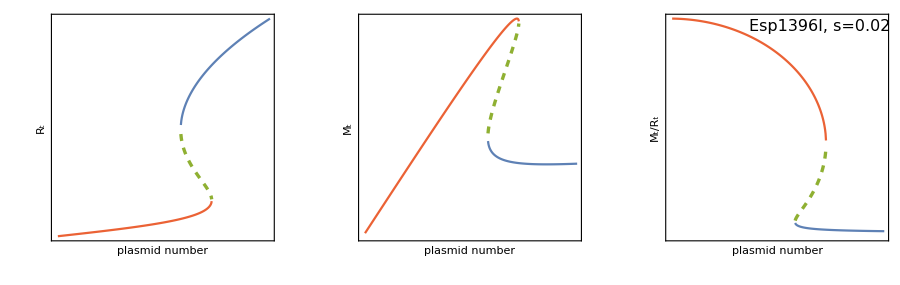

```mathematica
GraphicsRow[{PlotREsp,PlotMEsp,PlotMREsp},ImageSize->900]
```